# Interacting Dark Energy with a Quadratic EoS with a Late-Time Cosmological Constant

## Manipulate Plots

#### Non-Compact x - z Phase Space

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Find the condition for the repellor fixed point to be complex*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{wx}]
```

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[wx_,q_,ϵ_,ℛ_]=dex;
DM[q_]=dez;
```

```mathematica
0.7957951395478502<q<14.27996436870235
```

```mathematica
(*Plot the phase space for the dark energy and the dark matter with the boundary between accelerating and decelerating regions*)
Manipulate[Show[ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,3},{x,-.1,5},ContourStyle->Red],StreamPlot[{DM[q],DE[wx,q,ϵ,ℛ]},{z,0,3},{x,-.1,5},AxesLabel->{"z","x"}]],{q,0,300,Appearance->"Open"},{wx,-2,2,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
(*Set q = 1 to simplify the eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]/.{q->1}
```

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[q_,wx_,ϵ_,ℛ_]=de1;
H[wx_,ϵ_,ℛ_]=de2;
DM[q_]=de3;
```

```mathematica
(*Plot the x-y-z phase space*)
Manipulate[StreamPlot3D[{DE[q,wx,ϵ,ℛ],H[wx,ϵ,ℛ],DM[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

## Flat Submanifold

```mathematica
(*Define the system of differential equations*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Define the acceleration equation*)
AccnFlatGeneral[ℛ_]=z+xFlat*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*xFlat^2
```

```mathematica
(*Define x from the Friedmann equation when k = 0*)
xFlat=3*y^2-z
```

```mathematica
(*Re-define the acceleration equation in terms of y and z only, setting y = 0 in order to find the Einstein fixed points*)
AccnFlatEPtsGeneral[ℛ_]=AccnFlatGeneral[ℛ]/.y->0
```

```mathematica
(*Solve the a'' = 0 for ℛ*)
Solve[AccnFlatEPtsGeneral[ℛ]==0,ℛ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
(*Define parameters*)
(*Here wx > -1 + ℛ, but in order for this to be true when ℛ = 0 we define wx = -0.99 + γℛ *)
ϵ=-1;
wx=-0.9+γ*ℛ;
γ=10;
```

```mathematica
(*Redefine the acceleration equation with the parameters defined*)
AccnFlat[ℛ_]=AccnFlatGeneral[ℛ]
```

```mathematica
(*Redefine the equation to find the Einstein fixed points with the parameters defined*)
AccnFlatEPts[ℛ_]=AccnFlatEPtsGeneral[ℛ]
```

```mathematica
(*Solve the equation to find the Einstein fixed points for ℛ*)
Solve[AccnFlatEPts[ℛ]==0,ℛ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Re-define dey and dez in the flat case*)
deyFlat[ℛ_]=dey/.x->xFlat;
dezFlat[ℛ_]=dez/.x->xFlat;
```

```mathematica
(*Define q*)
q=10;
```

```mathematica
(*Solve dey and dez in the flat case for the fixed points*)
Solve[{dezFlat[ℛ]==0,deyFlat[ℛ]==0},{z,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Plot the equation to find the Einstein points*)
(*When the curve crosses the x-axis, there is an Einstein fixed point*)
AccnFlatCase=Manipulate[Plot[AccnFlatEPts[ℛ],{z,0,3},PlotStyle->Red],{ℛ,0,1,Appearance->"Open"}]
```

```mathematica
(*Plot the phase space in the flat case along with a'' = 0 (red) and the boundary where x = 0 (green)*)
Manipulate[Show[ContourPlot[AccnFlat[ℛ]==0,{z,0,3},{y,-3,3},ContourStyle->Red],ContourPlot[xFlat==0,{z,0,3},{y,-3,3},ContourStyle->Darker[Green]],StreamPlot[{dezFlat[ℛ],deyFlat[ℛ]},{z,0,3},{y,-3,3},AxesLabel->{"z","y"}]],{ℛ,0,1,Appearance->"Open"}]
```

## Find the Parameter Space

We want to find the cases where we have a repellor fixed point at a high dark energy density, and a low-energy attractor. In this section, we consider wx > -1 and wx < -1, for both ϵ = +1 and ϵ = -1. We then investigate the possible cases by varying q. We assume ℛ ~ 10^(-120)  to 10^(-100), although we use a much larger value to produce readable phase spaces.

## wx < -1, ϵ = +1

```mathematica
(*Define ϵ*)
ϵ=1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx<-1,wx]
```

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&0<q<3/ℛ&&-1-ℛ<wx<-1,q]
```

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/ℛ&&-1-ℛ<wx<-1,q]
```

```mathematica
(*Find the condition such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&-1-ℛ<wx<-1&&0<q<3/ℛ,q]
```

So, the fixed points at x = 3/q and at x = ℛ cannot both exist for x > 0, z > 0 where the x = ℛ fixed point is an attractor and the x = 3/q fixed point is a repellor. In general, the x = 3/q fixed point will not exist for z > 0 when the fixed point at x = ℛ is an attractor.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&-1-ℛ<wx<-1,w]
```

Therefore, the phase space has two fixed points. The (0,ℛ) fixed point has a larger x value than the x = (-1-1x)/ϵ  fixed point if (0,ℛ) is an attractor. This does not give us the desired topology.

## wx < -1, ϵ = -1

```mathematica
(*Define ϵ*)
ϵ=-1;
```

```mathematica
(*Find the value of wx needed for the first eigenvalue of the (0,ℛ) fixed point to be negative*)
Reduce[-3 (1+wx+ℛ* ϵ)<0,wx]
```

Therefore when ϵ = -1, w > - 1 + ℛ  for the (0,ℛ) fixed point to be an attractor. This excludes wx < -1 for ℛ > 0, which we assume here.

## wx > -1, ϵ = +1

```mathematica
(*Define ϵ*)
ϵ=1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx>-1&&ℛ>0,wx]
```

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&0<q<3/ℛ&&wx>-1,q]
```

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/ℛ&&wx>-1,q]
```

```mathematica
(*Find the condition such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&wx>-1&&0<q<3/ℛ,q]
```

So, the fixed points at x = 3/q and at x = ℛ cannot both exist for x > 0, z > 0 where the x = ℛ fixed point is an attractor and the x = 3/q fixed point is a repellor. In general, the x = 3/q fixed point will not exist for z > 0 when the fixed point at x = ℛ is an attractor.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&wx>-1&&ℛ>0,w]
```

The (0,(-1-wx)/ϵ) fixed point always has a smaller x value that the (0,ℛ) fixed point, which does not provide us with the desired topology.

## wx > -1, ϵ = -1

```mathematica
(*Define ϵ*)
ϵ=-1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx>-1&&0<ℛ<1,wx]
```

0<ℛ<1&&wx>-1+ℛ

```mathematica
qAttractorCondition=Reduce[-3+q ℛ<0&&0<ℛ<1,q]
```

0<ℛ<1&&q<3/ℛ

```mathematica
(*Define wx such that the (0,ℛ) fixed point is an attractor*)
(*γ > 1*)
wx=-1+γ*ℛ;
```

### 3 Fixed Points

```mathematica
(*Find the condition such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor*)
ThreeFixedPointsCondition=Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&0<ℛ<1&&γ > 1&&0<q<3/ℛ,q]
```

γ>1&&0<ℛ<1&&0<q<3/(ℛ γ)

For γ > 1 (wx > -1 + ℛ),  < 3/ℛ, so we use this more stringent condition to find the values of q for which the x =3/q fixed point has z > 0 and is a repellor.

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
RepellorCondition=Reduce[1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&0<q<3/(ℛ γ) &&γ > 1&&0<ℛ<1,q]
```

γ>1&&((0<ℛ<1/γ&&(0<q≤Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,1]||Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,2]≤q<3/(ℛ γ)))||(1/γ≤ℛ<1&&0<q<3/(ℛ γ)))

```mathematica
(*Here, no extra condition imposed. Still γ > 1, 0 < ℛ < 1 and 0 < q < 3/(ℛ γ), just in different combinations*)
```

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
SpiralRepellorCondition=Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ)/2*q>0&&(1/(2*q))*((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ))<0&&0<q<3/(ℛ γ)&&γ > 1&&0<ℛ<1,q]
```

γ>1&&0<ℛ<1/γ&&Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,1]<q<Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,2]

```mathematica
(*Here the assumption is that the eigenvalues are real, positive and the same*)
ImproperNodeCondition=Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ)/2*q>0&&(1/(2*q))*((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ))==0&&0<q<3/(ℛ γ)&&γ > 1&&0<ℛ<1,q]
```

γ>1&&((0<ℛ<1/γ&&(q==Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,1]||q==Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,2]))||(ℛ==1/γ&&q==Root[81-108 #1+(36 ℛ+36 ℛ γ-18 ℛ^2 γ) #1^2-12 ℛ^2 γ #1^3+ℛ^4 γ^2 #1^4&,1]))

So the conditions γ > 1, 0 < ℛ < 1 and 0 < q < 3/(ℛ γ) are sufficient for the x  = 3/q fixed point to be a repellor, but the stability of this fixed point changes depending on the combination of parameter constraints used, and can be a (non-)spiral repellor, or an improper node. In general, there are a range of q values where both the x = ℛ and x=3/q fixed point exist for x > 0 and z > 0, where the x = ℛ fixed point is an attractor, and the x = 3/q point is a (non-)spiral repellor. We now need to fix ℛ and wx.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&0<ℛ<1&&γ > 1,w]
```

γ>1&&0<ℛ<1

This means that the saddle always has a larger x-value than the x-value of the attractor for the parameter values we consider here.

```mathematica
(*Find where the a'' = 0 curve intercepts the x-axis*)
xIntercept=Simplify[Solve[x*(1+3*(-1+γ*ℛ)-3*ϵ*ℛ)-3*ℛ*(1+(-1+γ*ℛ))+3*ϵ*x^2==0,x] ]
```

{{x→1/6 (-2+3 ℛ (1+γ)-√(4+9 ℛ^2 (-1+γ)^2-12 ℛ (1+γ)))},{x→1/6 (-2+3 ℛ (1+γ)+√(4+9 ℛ^2 (-1+γ)^2-12 ℛ (1+γ)))}}

```mathematica
xIntercept1=x/.xIntercept[[1]]
xIntercept2=x/.xIntercept[[2]]
```

1/6 (-2+3 ℛ (1+γ)-√(4+9 ℛ^2 (-1+γ)^2-12 ℛ (1+γ)))

1/6 (-2+3 ℛ (1+γ)+√(4+9 ℛ^2 (-1+γ)^2-12 ℛ (1+γ)))

```mathematica
(*Find where the intercept is above ℛ so there is no late-time acceleration*)
```

```mathematica
NoAccnCondition1=Reduce[xIntercept1>ℛ&&0<ℛ<1&&γ>1&&wx<0]
```

γ>3 (5+2 √6)&&4/3 √(γ/(-1+γ)^4)+(2 (1+γ))/(3 (-1+γ)^2)≤ℛ<1/γ

```mathematica
NoAccnCondition2=Reduce[xIntercept2>ℛ&&0<ℛ<1&&γ>1&&wx<0]
```

γ>3 (5+2 √6)&&4/3 √(γ/(-1+γ)^4)+(2 (1+γ))/(3 (-1+γ)^2)≤ℛ<1/γ

```mathematica
(*Find the condition on γ*)
N[3 (5+2 √6),10]
```

29.69693846

```mathematica
ℛMinNoAccn=N[4/3 √(γ/(-1+γ)^4)+(2 (1+γ))/(3 (-1+γ)^2),5];
ℛMaxNoAccn=N[1/γ,3];
```

```mathematica
(*Find where the intercept is below ℛ so there is late-time acceleration*)
```

```mathematica
AccnCondition1=Reduce[xIntercept1<ℛ&&0<ℛ<1&&γ>1&&wx<0]
```

γ>1&&0<ℛ≤-4/3 √(γ/(-1+γ)^4)+(2 (1+γ))/(3 (-1+γ)^2)

```mathematica
AccnCondition2=Reduce[xIntercept2<ℛ&&0<ℛ<1&&γ>1&&wx<0]
```

γ>1&&0<ℛ≤-4/3 √(γ/(-1+γ)^4)+(2 (1+γ))/(3 (-1+γ)^2)

```mathematica
ℛMaxAccn=N[-4/3 √(γ/(-1+γ)^4)+(2 (1+γ))/(3 (-1+γ)^2),5];
```

#### No late - time acceleration

```mathematica
(*Set ℛ and γ such that there is no late-time acceleration*)
γ=100;
wx=-1+γ*ℛ;
```

```mathematica
(*Need to find R from condition above*)
```

```mathematica
ℛMinNoAccn
```

0.00823

```mathematica
ℛMaxNoAccn
```

1/100

```mathematica
N[1/(γ=10^(20)),5]
```

1.×10^-20

```mathematica
ℛ=0.008;
```

```mathematica
NoAccnCondition1
```

False

```mathematica
NoAccnCondition2
```

False

```mathematica
AccnCondition1
```

False

```mathematica
AccnCondition2
```

False

```mathematica
(*Find q such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

qAttractorCondition
```

q<375.

```mathematica
(*Find the values of q such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor*)
ThreeFixedPointsCondition
```

0<q<3.75×10^-18

```mathematica
(*Find the values of q for each stability of the x = 3/q fixed point*)
```

```mathematica
SpiralRepellorCondition
```

False

```mathematica
RepellorCondition
```

0<q<3.75×10^-18

```mathematica
ImproperNodeCondition
```

False

For   < q <   and   < q <   the fixed point at x = 3/q is a repellor, and for   < q < it is a spiral repellor.

```mathematica
Reduce[x*(1+3*(-1+γ*ℛ)-3*ϵ*ℛ)-3*ℛ*(1+(-1+γ*ℛ))+3*ϵ*x^2==0&&x<ℛ&&γ>1]
```

False

```mathematica
(*In this case, there is not always late-time accn*)
Reduce[x*(1+3*(-1+γ*ℛ)-3*ϵ*ℛ)-3*ℛ*(1+(-1+γ*ℛ))+3*ϵ*x^2==0&&x>ℛ]
```

x==8.×10^17

```mathematica
(*Find the x-intercept of the a'' = 0 curve at z = 0*)
(*If x is complex or imaginary, the a'' = 0 curve does not cross z = 0*)
(*This means there is not always late-time acceleration*)
xIntercept1
xIntercept2
```

0.

8.×10^17

#### Late - time acceleration

```mathematica
(*Set ℛ and γ such that there is late-time acceleration*)
γ=1.1;
wx=-1+γ*ℛ;
```

```mathematica
ℛMaxAccn
```

0.15882

```mathematica
ℛ=0.15;
```

```mathematica
(*For no late-time accn (x-intercept above ℛ) have to have γ > 3.3 and 0.143 <= ℛ < 1*)
```

```mathematica
NoAccnCondition1
```

False

```mathematica
NoAccnCondition2
```

False

```mathematica
(*For late-time accn (x-intercept below ℛ) have to have γ > 1 and 0 < ℛ ≤ 0.0385*)
(*which we don't have here*)
```

```mathematica
AccnCondition1
```

True

```mathematica
AccnCondition2
```

True

```mathematica
(*Find q such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

qAttractorCondition
```

q<20.

```mathematica
(*Find the values of q such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor*)
ThreeFixedPointsCondition
```

0<q<18.1818

```mathematica
(*Find the values of q for each stability of the x = 3/q fixed point*)
```

```mathematica
SpiralRepellorCondition
```

0.815615<q<18.1045

```mathematica
RepellorCondition
```

0<q≤0.815615||18.1045≤q<18.1818

```mathematica
ImproperNodeCondition
```

q==0.815615||q==18.1045

For  0 < q ≤   and  ≤ q <   the fixed point at x = 3/q is a repellor, and for  < q <   it is a spiral repellor.

```mathematica
Reduce[x*(1+3*(-1+γ*ℛ)-3*ϵ*ℛ)-3*ℛ*(1+(-1+γ*ℛ))+3*ϵ*x^2==0&&x<ℛ&&γ>1]
```

x==-0.254366||x==-0.0973008

```mathematica
(*In this case, there is always late-time accn*)
Reduce[x*(1+3*(-1+γ*ℛ)-3*ϵ*ℛ)-3*ℛ*(1+(-1+γ*ℛ))+3*ϵ*x^2==0&&x>ℛ]
```

False

```mathematica
(*Find the x-intercept of the a'' = 0 curve at z = 0*)
(*If x < ℛ, all trajectories have late-time acceleration*)
(*If x is complex or imaginary, the a'' = 0 curve does not cross z = 0 and all trajectories have late-time acceleration*)

xIntercept1
xIntercept2
```

-0.254366

-0.0973008

### 2 Fixed Points

The other possibility to explore is when 3/(1+wx)<q<3/ℛ. The x = 3/q fixed point does not exist at z > 0, however the (0, ℛ) fixed point is still an attractor, and the x = (-1-wx)/ϵ fixed point exists at x > 0.

```mathematica
(*Clear variables*)
Clear[wx,ℛ];
```

```mathematica
(*Find the conditions such that the x=(-1-wx)/ϵ fixed point is a repellor*)
Reduce[(-q-q wx-3 ϵ)/ϵ>0&&3 (1+wx+ℛ ϵ)>0&&3/(1+wx)<q<3/ℛ&&ℛ>0&&wx>-1+ℛ,wx]
```

ℛ>0&&0<q<3/ℛ&&wx>(3-q)/q

```mathematica
(*Find the condition on q such that the x=(-1-wx)/ϵ fixed point is a repellor*)
Reduce[(-q-q wx-3 ϵ)/ϵ>0&&3 (1+wx+ℛ ϵ)>0&&3/(1+wx)<q<3/ℛ,q]
```

ℛ>0&&wx>-1+ℛ&&3/(1+wx)<q<3/ℛ

For   < q < , two fixed points exist that satisfy x > 0 and z > 0, where the repellor has a larger x value than the attractor.

## Late-Time Acceleration

## Late-Time Deceleration

## Spiral Repellor Case

This is the case where 0.889947 < q < 5.18699.

## Full 2D and 3D phase spaces

```mathematica
0<q<18.18181818181818
```

```mathematica
0.8156153569870306<q<18.104519011670266
```

### Non-Compact x - z Phase Space: Separatrix and a’’ = 0 curve do cross

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,2Range[-1,25]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,2Range[0,55]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Set parameter values*)
ϵ=-1;
q=6;
```

```mathematica
(*Set ℛ and wx*)
ℛ=0.15;
γ=1.1;
wx=-1+γ*ℛ
```

-0.835

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzSpiral=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.15},{z→0.,x→0.165},{z→0.11725,x→0.5}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzSpiral[1]={z/.FPsxzSpiral[[1,1]],x/.FPsxzSpiral[[1,2]]};
FPxzSpiral[2]={z/.FPsxzSpiral[[2,1]],x/.FPsxzSpiral[[2,2]]};
FPxzSpiral[3]={z/.FPsxzSpiral[[3,1]],x/.FPsxzSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableSpiral=Table[FPxzSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzSpiral=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzSpiral//MatrixForm
```

(-3+6 x | 6 z
-6 x | 6. (-0.1575+x-1. z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPxzTableSpiral[[i]]//MatrixForm,Simplify[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.15) | (-2.1 | 0.
-0.9 | -0.045) | (-2.1
-0.045) | (0.916004 | 0.40117
0. | 1.)
(0.
0.165) | (-2.01 | 0.
-0.99 | 0.045) | (-2.01
0.045) | (0.900906 | 0.434013
0. | 1.)
(0.11725
0.5) | (0. | 0.7035
-3. | 1.3515) | (0.67575+1.28603 ⅈ
0.67575-1.28603 ⅈ) | (0.202731-0.385818 ⅈ | 0.900025+0. ⅈ
0.202731+0.385818 ⅈ | 0.900025+0. ⅈ)

```mathematica
(*Plot the fixed points*)
FPsxzSpiral=ListPlot[FPxzTableSpiral,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzSpiral=StreamPlot[{dez,dex},{z,0,55},{x,-1,25}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineSpiral=ContourPlot[-3*z + q*x*z==0,{z,-.1,55},{x,-1,25},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineSpiral=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,55},{x,-1,25},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzSpiral=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,55},{x,-1,25},ContourStyle->Red];
```

```mathematica
(*At z=0, x value of a''=0 curve*)
Solve[x*(1+3*(-1+γ1*ℛ1)-3*ϵ*ℛ1)-3*ℛ1*(1+(-1+γ1*ℛ1))+3*ϵ*x^2==0,x]
```

{{x→1/6 (-2+3 ℛ1+3 ℛ1 γ1-√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))},{x→1/6 (-2+3 ℛ1+3 ℛ1 γ1+√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))}}

```mathematica
Reduce[1/6 (-2+3 ℛ1+3 ℛ1 γ1-√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))<ℛ1&&γ1>1&&0<ℛ1<1&&-1<-1+γ1*ℛ1<0]
```

γ1>1&&0<ℛ1≤-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)

```mathematica
N[-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)/.γ1->10^(110),10]
```

6.666666667×10^-111

```mathematica
Reduce[1/6 (-2+3 ℛ1+3 ℛ1 γ1+√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))<ℛ1&&γ1>1&&0<ℛ1<1&&-1<-1+γ1*ℛ1<0]
```

γ1>1&&0<ℛ1≤-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)

```mathematica
N[-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)/.γ1->2,2]
```

0.11

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix between the repellor and saddle fixed point*)
SeparatrixSpiral=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

{{z1→InterpolatingFunction[…],x1→InterpolatingFunction[…]}}

```mathematica
(*Plot the separatrix*)
SeparatrixPlotSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixSpiral,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,55},{-1,25}}];
```

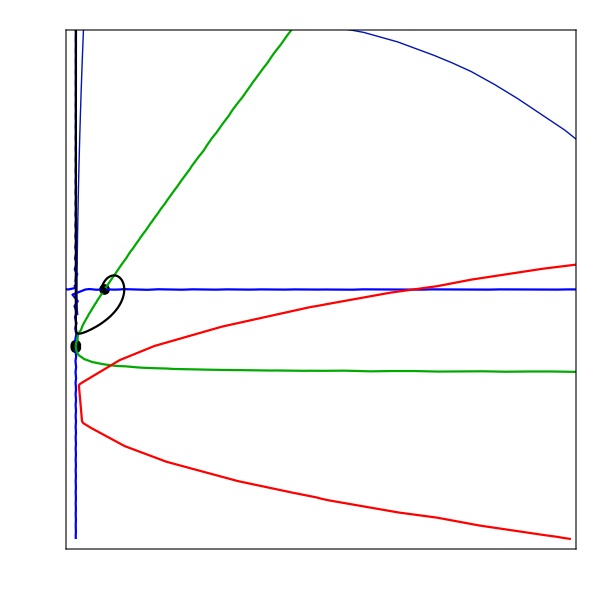

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzSpiral,FPsxzSpiral,zLineSpiral,xLineSpiral,AccnxzSpiral,SeparatrixPlotSpiral,xzFormat,PlotRange->{{0,2},{-1,2}}]
```

### Non-Compact x - z Phase Space: Separatrix and a’’ = 0 curve do not cross

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,7]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,1Range[0,10]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Set parameter values*)
ϵ=-1;
q=1.5;
```

```mathematica
(*Set ℛ and wx*)
ℛ=0.05;
γ=10;
wx=-1+γ*ℛ
```

-0.5

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzSpiral=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→0.,x→0.5},{z→2.925,x→2.}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzSpiral[1]={z/.FPsxzSpiral[[1,1]],x/.FPsxzSpiral[[1,2]]};
FPxzSpiral[2]={z/.FPsxzSpiral[[2,1]],x/.FPsxzSpiral[[2,2]]};
FPxzSpiral[3]={z/.FPsxzSpiral[[3,1]],x/.FPsxzSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableSpiral=Table[FPxzSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzSpiral=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzSpiral//MatrixForm
```

(-3+1.5 x | 1.5 z
-1.5 x | 6. (-0.275+x-0.25 z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPxzTableSpiral[[i]]//MatrixForm,Simplify[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.925 | 0.
-0.075 | -1.35) | (-2.925
-1.35) | (0.998868 | 0.0475651
0. | 1.)
(0.
0.5) | (-2.25 | 0.
-0.75 | 1.35) | (-2.25
1.35) | (0.97898 | 0.203954
0. | 1.)
(2.925
2.) | (0. | 4.3875
-3. | 5.9625) | (2.98125+2.06752 ⅈ
2.98125-2.06752 ⅈ) | (0.770655+0. ⅈ | 0.52365+0.363156 ⅈ
0.770655+0. ⅈ | 0.52365-0.363156 ⅈ)

```mathematica
(*Plot the fixed points*)
FPsxzSpiral=ListPlot[FPxzTableSpiral,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzSpiral=StreamPlot[{dez,dex},{z,0,7},{x,-1,4}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineSpiral=ContourPlot[-3*z + q*x*z==0,{z,-.1,7},{x,-1,4},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineSpiral=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,7},{x,-1,4},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzSpiral=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,7},{x,-1,4},ContourStyle->Red];
```

```mathematica
(*At z=0, x value of a''=0 curve*)
Solve[x*(1+3*(-1+γ1*ℛ1)-3*ϵ*ℛ1)-3*ℛ1*(1+(-1+γ1*ℛ1))+3*ϵ*x^2==0,x]
```

{{x→1/6 (-2+3 ℛ1+3 ℛ1 γ1-√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))},{x→1/6 (-2+3 ℛ1+3 ℛ1 γ1+√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))}}

```mathematica
Reduce[1/6 (-2+3 ℛ1+3 ℛ1 γ1-√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))<ℛ1&&γ1>1&&0<ℛ1<1&&-1<-1+γ1*ℛ1<0]
```

γ1>1&&0<ℛ1≤-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)

```mathematica
N[-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)/.γ1->10^(110),10]
```

6.666666667×10^-111

```mathematica
Reduce[1/6 (-2+3 ℛ1+3 ℛ1 γ1+√(-36 ℛ1^2 γ1+(-2+3 ℛ1+3 ℛ1 γ1)^2))<ℛ1&&γ1>1&&0<ℛ1<1&&-1<-1+γ1*ℛ1<0]
```

γ1>1&&0<ℛ1≤-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)

```mathematica
N[-4/3 √(γ1/(-1+γ1)^4)+(2 (1+γ1))/(3 (-1+γ1)^2)/.γ1->2,2]
```

0.11

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix between the repellor and saddle fixed point*)
SeparatrixSpiral=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

{{z1→InterpolatingFunction[…],x1→InterpolatingFunction[…]}}

```mathematica
(*Plot the separatrix*)
SeparatrixPlotSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixSpiral,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,7},{-1,4}}];
```

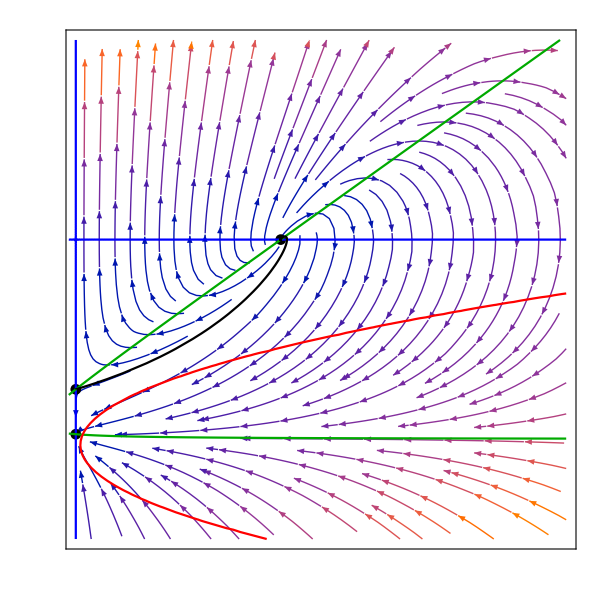

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzSpiral,FPsxzSpiral,zLineSpiral,xLineSpiral,AccnxzSpiral,SeparatrixPlotSpiral,xzFormat,PlotRange->{{0,7},{-1,4}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsSpiral=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.025 (3.+14. x+120. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→0.5,y→-0.408248,z→0.},{x→0.5,y→0.408248,z→0.},{x→2.,y→-1.28128,z→2.925},{x→2.,y→1.28128,z→2.925}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPSpiral[1]={x,y/.FPsSpiral[[1,1]],z/.FPsSpiral[[1,2]]};
FPSpiral[2]={x/.FPsSpiral[[2,1]],y/.FPsSpiral[[2,2]],z/.FPsSpiral[[2,3]]};
FPSpiral[3]={x/.FPsSpiral[[3,1]],y/.FPsSpiral[[3,2]],z/.FPsSpiral[[3,3]]};
FPSpiral[4]={x/.FPsSpiral[[4,1]],y/.FPsSpiral[[4,2]],z/.FPsSpiral[[4,3]]};
FPSpiral[5]={x/.FPsSpiral[[5,1]],y/.FPsSpiral[[5,2]],z/.FPsSpiral[[5,3]]};
FPSpiral[6]={x/.FPsSpiral[[6,1]],y/.FPsSpiral[[6,2]],z/.FPsSpiral[[6,3]]};
FPSpiral[7]={x/.FPsSpiral[[7,1]],y/.FPsSpiral[[7,2]],z/.FPsSpiral[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsSpiral=Table[FPSpiral[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzSpiral=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzSpiral//MatrixForm
```

(y (-1.65+6. x-1.5 z) | 3. (0.025+x^2+x (-0.55-0.5 z)) | -1.5 x y
0.0583333+x | -2 y | -1/6
1.5 y z | (-3+1.5 x) z | (-3+1.5 x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPsSpiral[[i]]//MatrixForm,Simplify[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexyzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.025 (3.+14. x+120. x^2)) | (0. | 0.075-1.7625 x+2.475 x^2-4.5 x^3 | 0.
0.0583333+x | 0. | -1/6
0. | -0.225-0.9375 x-8.475 x^2+4.5 x^3 | 0.) | (0
-√(0.041875+0.128438 x-0.205625 x^2+1.4625 x^3-4.5 x^4)
√(0.041875+0.128438 x-0.205625 x^2+1.4625 x^3-4.5 x^4)) | (0.166667/(0.0583333+x) | 0 | 1.
-(1. (-0.000972222+0.00618056 x+0.359583 x^2-0.491667 x^3+1. x^4))/((0.0583333+x) (-0.05-0.208333 x-1.88333 x^2+1. x^3)) | -(0.222222 √(0.041875+0.128437 x-0.205625 x^2+1.4625 x^3-4.5 x^4))/(-0.05-0.208333 x-1.88333 x^2+1. x^3) | 1.
-(1. (-0.000972222+0.00618056 x+0.359583 x^2-0.491667 x^3+1. x^4))/((0.0583333+x) (-0.05-0.208333 x-1.88333 x^2+1. x^3)) | (0.222222 √(0.041875+0.128437 x-0.205625 x^2+1.4625 x^3-4.5 x^4))/(-0.05-0.208333 x-1.88333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.174284 | 2.08167×10^-17 | 0.00968246
0.108333 | 0.258199 | -1/6
0. | 0. | 0.377616) | (0.377616
0.258199
0.174284) | (0.0282994 | -0.803755 | 0.594287
-1.15126×10^-16 | -1. | 0.
-0.612372 | 0.790569 | 0.)
(0.05
0.129099
0.) | (-0.174284 | 2.08167×10^-17 | -0.00968246
0.108333 | -0.258199 | -1/6
0. | 0. | -0.377616) | (-0.377616
-0.258199
-0.174284) | (0.0282994 | 0.803755 | 0.594287
-1.15126×10^-16 | 1. | 0.
0.612372 | 0.790569 | 0.)
(0.5
-0.408248
0.) | (-0.551135 | 1.66533×10^-16 | 0.306186
0.558333 | 0.816497 | -1/6
0. | 0. | 0.918559) | (0.918559
0.816497
-0.551135) | (0.183659 | -0.434875 | 0.881563
-1.7255×10^-16 | -1. | 0.
-0.92582 | 0.377964 | 0.)
(0.5
0.408248
0.) | (0.551135 | 1.66533×10^-16 | -0.306186
0.558333 | -0.816497 | -1/6
0. | 0. | -0.918559) | (-0.918559
-0.816497
0.551135) | (0.183659 | 0.434875 | 0.881563
-1.7255×10^-16 | 1. | 0.
0.92582 | 0.377964 | 0.)
(2.
-1.28128
2.925) | (-7.6396 | 2.66454×10^-15 | 3.84383
2.05833 | 2.56255 | -1/6
-5.6216 | 0. | 0.) | (-3.8198+2.64907 ⅈ
-3.8198-2.64907 ⅈ
2.56255+0. ⅈ) | (0.515823-0.357728 ⅈ | -0.165845+0.0465328 ⅈ | 0.759136+0. ⅈ
0.515823+0.357728 ⅈ | -0.165845-0.0465328 ⅈ | 0.759136+0. ⅈ
2.16224×10^-16+0. ⅈ | 1.+0. ⅈ | -3.62854×10^-16+0. ⅈ)
(2.
1.28128
2.925) | (7.6396 | 2.66454×10^-15 | -3.84383
2.05833 | -2.56255 | -1/6
5.6216 | 0. | 0.) | (3.8198+2.64907 ⅈ
3.8198-2.64907 ⅈ
-2.56255+0. ⅈ) | (0.515823+0.357728 ⅈ | 0.165845+0.0465328 ⅈ | 0.759136+0. ⅈ
0.515823-0.357728 ⅈ | 0.165845-0.0465328 ⅈ | 0.759136+0. ⅈ
2.16224×10^-16+0. ⅈ | -1.+0. ⅈ | -3.62854×10^-16+0. ⅈ)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineSpiral=ParametricPlot3D[{FPSpiral[1][[1]],FPSpiral[1][[2]],FPSpiral[1][[3]]},{x,0,4},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzSpiral=ListPointPlot3D[Table[FPSpiral[i],{i,2,7}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzSpiral=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,4},{y,-5,5},{z,0,7},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzSpiral=StreamPlot3D[{dex,dey,dez},{x,0,4},{y,-5,5},{z,0,7},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzSpiral,FPsxyzSpiral,EinsteinPointLineSpiral,AccnxyzSpiral,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,2.,4.,6.},{-5.,0.,1.,5.},{0.,2.,4.,6.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.},{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Plot the Flat Friedmann Separatrix (FFS)

```mathematica
(*Define the Friedmann equation when K = 0*)
yFFS=Sqrt[x/3+z/3];
```

```mathematica
(*Plot the FFS*)
FFSPlot=ParametricPlot3D[{{x,yFFS,z},{x,-yFFS,z}},{x,0,3},{z,0,3},PlotStyle->{Darker[Green]},Mesh->None];
```

```mathematica
(*Show the FFS*)
Show[FFSPlot,xyzFormat]
```

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingSpiral=0.0085;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0LimitingSpiral=y0/.z0->z0LimitingSpiral
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0LimitingSpiral,z1[0]==z0LimitingSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all x1 and z1 values to be used to find the x and z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSolLimitingSpiral=Table[x1[i]/.trajLimitingSpiral[0],{i,-100,100,.01}];
zTableSolLimitingSpiral=Table[z1[i]/.trajLimitingSpiral[0],{i,-100,100,.01}];
```

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingSpiral=(zTableSolLimitingSpiral)+(xTableSolLimitingSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimiting that is closest to zero. When EinsteinPlotValuesSolLimiting = 0 (y = 0), there is an Einstein point*)
NearestToZeroLimitingSpiral=Flatten[Nearest[EinsteinPlotValuesSolLimitingSpiral,0]]
```

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair 0 and ….

```mathematica
(*Find the position of NearestToZeroLimiting in the EinsteinPlotValuesSolLimiting array*)
PositionNearestToZeroLimitingSpiral=Flatten[Position[EinsteinPlotValuesSolLimitingSpiral,NearestToZeroLimitingSpiral]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSolLimiting and zTableSolLimiting at PositionNearestToZeroLimiting*)
EinsteinPointLimitingSpiral=Flatten[{xTableSolLimitingSpiral[[PositionNearestToZeroLimitingSpiral]],0,zTableSolLimitingSpiral[[PositionNearestToZeroLimitingSpiral]]}]
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingSpiral=Table[{EinsteinPointLimitingSpiral//MatrixForm,Simplify[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm},1];
```

Part::partw: Part 2 of {0} does not exist.

Part::partw: Part 3 of {0} does not exist.

Part::partw: Part 2 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingSpiral=TableForm[EinsteinTableLimitingSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all x1 and z1 values with a bigger t increment*)
xTableSolLimitingFullSpiral=Table[x1[i]/.trajLimitingSpiral[0],{i,-100,100,.1}];
zTableSolLimitingFullSpiral=Table[z1[i]/.trajLimitingSpiral[0],{i,-100,100,.1}];
```

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3 (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[«1»]^2+1/6 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolLimitingFullSpiral=(zTableSolLimitingFullSpiral)+(xTableSolLimitingFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolLimitingFull values and the EinsteinPlotValuesSolLimitingFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingSpiral=MapThread[h,{xTableSolLimitingFullSpiral,EinsteinPlotValuesSolLimitingFullSpiral}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotLimitingSpiral=ListPlot[EinsteinPointSolutionsLimitingSpiral,PlotRange->{{0,1.5},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3. (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-1. y1[«1»]^2+0.1666666666666667 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3. y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3. (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-1. y1[«1»]^2+0.1666666666666667 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3. y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition 2. ℛ is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x1'[t]==-3. (Times[«2»]+Times[«2»]) (Times[«2»]+x1[«1»]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-1. y1[«1»]^2+0.1666666666666667 (Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]),z1'[t]==-3. y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==2. ℛ,y1[0]==√(0.00283333+0.666667 ℛ),z1[0]==0.0085},{x1,y1,z1},{t,-100.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxLimitingSpiral=K/.Solve[y0LimitingSpiral==0,K][[1]]
```

```mathematica
(*Solve trajLimiting[K] for different values of K*)
```

```mathematica
solLimitingSpiral[1]=trajLimitingSpiral[0.01]
```

```mathematica
solLimitingSpiral[2]=trajLimitingSpiral[KDensityParametersClosed]
```

```mathematica
solLimitingSpiral[3]=trajLimitingSpiral[-.1]
```

NDSolve::ndsz: At t == -2.89319, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solLimitingSpiral[4]=trajLimitingSpiral[0.015]
```

```mathematica
solLimitingSpiral[5]=trajLimitingSpiral[-0.01]
```

NDSolve::ndsz: At t == -5.99158, step size is effectively zero; singularity or stiff system suspected.

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajLimitingxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[3],{t,-2.88,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajLimitingxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[5],{t,-5.98,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseSpiral=Table[trajLimitingxyzSpiral[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingSpiral=ListPointPlot3D[{EinsteinPointLimitingSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimitingSpiral[[1]],y1[0]==0,z1[0]==EinsteinPointLimitingSpiral[[3]]},{x1,y1,z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSLimitingSpiral=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSolSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajLimitingCaseSpiral,EinsteinFixedPointsLimitingSpiral,CFSLimitingSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,3},{-5,5},{0,4}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajLimitingxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solLimitingSpiral[2],{t,-100,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the x-z plane*)
EinsteinFixedPointsLimitingxzSpiral=ListPlot[{{EinsteinPointLimitingSpiral[[3]],EinsteinPointLimitingSpiral[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajLimitingxzSpiral,xLineSpiral,zLineSpiral,AccnxzSpiral,FPsxzSpiral,EinsteinFixedPointsLimitingxzSpiral,xzFormat,PlotRange->{{0,3.5},{0,2.5}}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsSpiral=Ωm0*ℛ/(Ωx0*α)
```

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsSpiral=y0/.z0->z0TwoEinsteinPointsSpiral
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsSpiral,z1[0]==z0TwoEinsteinPointsSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsSpiral=(zTableSol1TwoEinsteinPointsSpiral)+(xTableSol1TwoEinsteinPointsSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Spiral=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsSpiral,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Spiral=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsSpiral,NearestToZeroTwoEinsteinPoints1Spiral]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsSpiral=Flatten[{xTableSol1TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints1Spiral]],0,zTableSol1TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints1Spiral]]}]
```

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsSpiral=(zTableSol2TwoEinsteinPointsSpiral)+(xTableSol2TwoEinsteinPointsSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Spiral=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsSpiral,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Spiral=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsSpiral,NearestToZeroTwoEinsteinPoints2Spiral]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsSpiral=Flatten[{xTableSol2TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints2Spiral]],0,zTableSol2TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints2Spiral]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsSpiral[1]=EinsteinPoint1TwoEinsteinPointsSpiral;
EinsteinPointTwoEPtsSpiral[2]=EinsteinPoint2TwoEinsteinPointsSpiral;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsSpiral=Table[EinsteinPointTwoEPtsSpiral[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsSpiral=Table[{EinsteinPointsTwoEPtsSpiral[[i]]//MatrixForm,Simplify[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsSpiral=TableForm[EinsteinPointTableTwoEinsteinPointsSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFullSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullSpiral=(zTableSolTwoEinsteinPointsFullSpiral)+(xTableSolTwoEinsteinPointsFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsSpiral=MapThread[h,{xTableSolTwoEinsteinPointsFullSpiral,EinsteinPlotValuesSolTwoEinsteinPointsFullSpiral}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsSpiral=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsSpiral,PlotRange->{{0,1.5},{-3,1.5}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsSpiral=K/.Flatten[Solve[y0TwoEinsteinPointsSpiral==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsSpiral[1]=trajTwoEinsteinPointsSpiral[-.02]
```

NDSolve::ndsz: At t == -4.21647, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsSpiral[2]=trajTwoEinsteinPointsSpiral[0.005]
```

```mathematica
solTwoEinsteinPointsSpiral[3]=trajTwoEinsteinPointsSpiral[-.1]
```

NDSolve::ndsz: At t == -2.68568, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsSpiral[4]=trajTwoEinsteinPointsSpiral[KMaxTwoEinsteinPointsSpiral]
```

```mathematica
solTwoEinsteinPointsSpiral[5]=trajTwoEinsteinPointsSpiral[0.03]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[1],{t,-4.21,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[3],{t,-2.65,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsSpiral[[1]],y1[0]==0.3,z1[0]==EinsteinPoint2TwoEinsteinPointsSpiral[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzSpiral[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsSpiral,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseSpiral=Table[trajTwoEinsteinPointsxyzSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsSpiral=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsSpiral,EinsteinPoint2TwoEinsteinPointsSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsSpiral[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsSpiral[[3]]},{x1,y1,z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsSpiral=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseSpiral,CFSTwoEinsteinPointsSpiral,EinsteinFixedPointsTwoEinsteinPointsSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,3},{-5,5},{0,4}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsSpiral[1],{t,-4.21,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzSpiral=ListPlot[{{EinsteinPoint1TwoEinsteinPointsSpiral[[3]],EinsteinPoint1TwoEinsteinPointsSpiral[[1]]},{EinsteinPoint2TwoEinsteinPointsSpiral[[3]],EinsteinPoint2TwoEinsteinPointsSpiral[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzSpiral,AccnxzSpiral,xLineSpiral,zLineSpiral,FPsxzSpiral,EinsteinFixedPointsTwoEinsteinPointsxzSpiral,xzFormat,PlotRange->{{0,4},{0,2.5}}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsSpiral=0.005;
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPointsSpiral=y0/.z0->z0NoEinsteinPointsSpiral
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPointsSpiral,z1[0]==z0NoEinsteinPointsSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.035-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolNoEinsteinPointsFullSpiral=Table[x1[i]/.trajNoEinsteinPointsSpiral[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFullSpiral=Table[z1[i]/.trajNoEinsteinPointsSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullSpiral=(zTableSolNoEinsteinPointsFullSpiral)+(xTableSolNoEinsteinPointsFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolNoEinsteinPointsFull values and the EinsteinPlotValuesSolNoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsSpiral=MapThread[h,{xTableSolNoEinsteinPointsFullSpiral,EinsteinPlotValuesSolNoEinsteinPointsFullSpiral}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*Here, f(x,z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsSpiral=ListPlot[EinsteinPointSolutionsNoEinsteinPointsSpiral,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxNoEinsteinPointsSpiral=K/.Solve[y0NoEinsteinPointsSpiral==0,K][[1]]
```

```mathematica
(*Solve trajNoEinsteinPoints[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsSpiral[1]=trajNoEinsteinPointsSpiral[-0.01]
```

NDSolve::ndsz: At t == -6.26236, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solNoEinsteinPointsSpiral[2]=trajNoEinsteinPointsSpiral[KDensityParametersClosed]
```

```mathematica
solNoEinsteinPointsSpiral[3]=trajNoEinsteinPointsSpiral[-.08]
```

NDSolve::ndsz: At t == -3.20889, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solNoEinsteinPointsSpiral[4]=trajNoEinsteinPointsSpiral[0.0095]
```

```mathematica
solNoEinsteinPointsSpiral[5]=trajNoEinsteinPointsSpiral[0.007]
```

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[1],{t,-6.25,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[3],{t,-3.2,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsSpiral=Table[trajNoEinsteinPointsxyzSpiral[i],{i,1,5}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajNoEinsteinPointsPlotsSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,2.5},{-5,5},{0,4}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajNoEinsteinPointsxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solNoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsxzSpiral,xLineSpiral,zLineSpiral,AccnxzSpiral,FPsxzSpiral,xzFormat,PlotRange->{{0,3.5},{0,2.5}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=1.5;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZSpiral=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZSpiral[1]={X,Y/.FPsXYZSpiral[[1,1]],Z/.FPsXYZSpiral[[1,2]]};
FPXYZSpiral[2]={X/.FPsXYZSpiral[[2,1]],Y/.FPsXYZSpiral[[2,2]],Z/.FPsXYZSpiral[[2,3]]};
FPXYZSpiral[3]={X/.FPsXYZSpiral[[3,1]],Y/.FPsXYZSpiral[[3,2]],Z/.FPsXYZSpiral[[3,3]]};
FPXYZSpiral[4]={X/.FPsXYZSpiral[[6,1]],Y/.FPsXYZSpiral[[6,2]],Z/.FPsXYZSpiral[[6,3]]};
FPXYZSpiral[5]={X/.FPsXYZSpiral[[7,1]],Y/.FPsXYZSpiral[[7,2]],Z/.FPsXYZSpiral[[7,3]]};
FPXYZSpiral[6]={X/.FPsXYZSpiral[[8,1]],Y/.FPsXYZSpiral[[8,2]],Z/.FPsXYZSpiral[[8,3]]};
FPXYZSpiral[7]={X/.FPsXYZSpiral[[9,1]],Y/.FPsXYZSpiral[[9,2]],Z/.FPsXYZSpiral[[9,3]]};
FPXYZSpiral[8]={X/.FPsXYZSpiral[[10,1]],Y/.FPsXYZSpiral[[10,2]],Z/.FPsXYZSpiral[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableSpiral=Table[FPXYZSpiral[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZSpiral=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZSpiral//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactSpiral=Table[{FPXYZTableSpiral[[i]]//MatrixForm,Simplify[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZSpiral=TableForm[FPTableCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXYZSpiral=ListPointPlot3D[Table[FPXYZSpiral[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroSpiral=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeSpiral=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroSpiral][[1]]
```

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolSpiral=X/.FindRoot[ZPrimeSpiral==0,{X,0.75}]
```

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolSpiral=Flatten[ZXPrimeZeroSpiral/.X->XdSSolSpiral][[1]]
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZSpiral=ListPointPlot3D[{{XdSSolSpiral,1,ZdSSolSpiral},{XdSSolSpiral,-1,ZdSSolSpiral}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactSpiral=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZSpiral=ContourPlot3D[AccnCompactSpiral==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZSpiral=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZSpiral[1]={Z/.FPsXZSpiral[[1,1]],X/.FPsXZSpiral[[1,2]]};
FPXZSpiral[2]={Z/.FPsXZSpiral[[2,1]],X/.FPsXZSpiral[[2,2]]};
FPXZSpiral[3]={Z/.FPsXZSpiral[[3,1]],X/.FPsXZSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableSpiral=Table[FPXZSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZSpiral=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZSpiral//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactSpiral=Table[{FPXZTableSpiral[[i]]//MatrixForm,Simplify[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZSpiral=TableForm[FPTableCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXZSpiral=ListPlot[FPXZTableSpiral, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZSpiral=ListPlot[{{ZdSSolSpiral,XdSSolSpiral}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZSpiral=ContourPlot[AccnCompactSpiral==0,{Z,0,1},{X,0,1},ContourStyle->{Red},Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineSpiral=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineSpiral=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Plot the Flat Friedmann Separatrix (FFS)

```mathematica
(*Define the Friedmann equation when K = 0 in terms of compact variables*)
yFFS=Sqrt[X/(3*(1-X))+Z/(3*(1-Z))];
```

```mathematica
(*Compactify yFFS*)
YFFS=yFFS/Sqrt[1+yFFS^2];
```

```mathematica
(*Plot the FFS*)
FFSCompactPlot=ParametricPlot3D[{{X,YFFS,Z},{X,-YFFS,Z}},{X,0,1},{Z,0,1},PlotStyle->{Darker[Green]},Mesh->None];
```

```mathematica
(*Show the FFS*)
Show[FFSCompactPlot,XYZCompactFormat]
```

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingSpiral=0.0085;
```

```mathematica
(*Compactify z0*)
Z0LimitingSpiral=z0LimitingSpiral/(1+z0LimitingSpiral)
```

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0LimitingSpiral=Y0/.Z0->Z0LimitingSpiral
```

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingSpiral,Z1[0]==Z0LimitingSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0361667-1. K))/(√(1.03617-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values to be used to find the X and Z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSolLimitingCompactSpiral=Table[X1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.01}];
ZTableSolLimitingCompactSpiral=Table[Z1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingCompactSpiral=(ZTableSolLimitingCompactSpiral/(1-ZTableSolLimitingCompactSpiral))+(XTableSolLimitingCompactSpiral/(1-XTableSolLimitingCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompactSpiral/(1-XTableSolLimitingCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimitingCompact that is closest to zero. When EinsteinPlotValuesSolLimitingCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroLimitingCompactSpiral=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompactSpiral,0]]
```

```mathematica
(*Find the position of NearestToZeroLimitingCompact in the EinsteinPlotValuesSolLimitingCompact array*)
PositionNearestToZeroLimitingCompactSpiral=Flatten[Position[EinsteinPlotValuesSolLimitingCompactSpiral,NearestToZeroLimitingCompactSpiral]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSolLimitingCompact and ZTableSolLimitingCompact at PositionNearestToZeroLimitingCompact*)
EinsteinPointLimitingCompactSpiral=Flatten[{XTableSolLimitingCompactSpiral[[PositionNearestToZeroLimitingCompactSpiral]],0,ZTableSolLimitingCompactSpiral[[PositionNearestToZeroLimitingCompactSpiral]]}]
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingCompactSpiral=Table[{EinsteinPointLimitingCompactSpiral//MatrixForm,Simplify[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingCompactSpiral=TableForm[EinsteinTableLimitingCompactSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all X1 and Z1 values with a bigger t increment*)
XTableSolLimitingFullCompactSpiral=Table[X1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.1}];
ZTableSolLimitingFullCompactSpiral=Table[Z1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolLimitingFullXZSpiral=(ZTableSolLimitingFullCompactSpiral/(1-ZTableSolLimitingFullCompactSpiral))+(XTableSolLimitingFullCompactSpiral/(1-XTableSolLimitingFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompactSpiral/(1-XTableSolLimitingFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolLimitingFullXZ*)
EinsteinPlotValuesSolLimitingFullCompactSpiral=EinsteinPlotValuesSolLimitingFullXZSpiral/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZSpiral^2];
```

```mathematica
(*Merge the XTableSolLimitingFullCompact values and the EinsteinPlotValuesSolLimitingFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompactSpiral=MapThread[h,{XTableSolLimitingFullCompactSpiral,EinsteinPlotValuesSolLimitingFullCompactSpiral}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotLimitingCompactSpiral=ListPlot[EinsteinPointSolutionsLimitingCompactSpiral,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxLimitingCompactSpiral=K/.Solve[Y0LimitingSpiral==0,K][[1]]
```

```mathematica
(*Solve trajLimitingCompact[K] for different values of K*)
```

```mathematica
solLimitingCompactSpiral[1]=trajLimitingCompactSpiral[0.01]
```

```mathematica
solLimitingCompactSpiral[2]=trajLimitingCompactSpiral[KDensityParametersClosed]
```

```mathematica
solLimitingCompactSpiral[3]=trajLimitingCompactSpiral[-.1]
```

NDSolve::mxst: Maximum number of 420165 steps reached at the point t == -2.89735.

```mathematica
solLimitingCompactSpiral[4]=trajLimitingCompactSpiral[0.015]
```

```mathematica
solLimitingCompactSpiral[5]=trajLimitingCompactSpiral[-0.01]
```

NDSolve::mxst: Maximum number of 156680 steps reached at the point t == -6.00323.

```mathematica
solLimitingCompactSpiral[6]=trajLimitingCompactSpiral[0.013]
```

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajLimitingCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[3],{t,-2.88,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[5],{t,-5.98,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseCompactSpiral=Table[trajLimitingCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingCompactSpiral=ListPointPlot3D[{EinsteinPointLimitingCompactSpiral},PlotStyle->Black];
```

```mathematica
(*Solve theX-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompactSpiral[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSLimitingCompactSpiral=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompactSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajLimitingCaseCompactSpiral,EinsteinFixedPointsLimitingCompactSpiral,CFSLimitingCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajLimitingCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solLimitingCompactSpiral[3],{t,-2.89,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the X-Z plane*)
EinsteinFixedPointsLimitingCompactXZSpiral=ListPlot[{{EinsteinPointLimitingCompactSpiral[[3]],EinsteinPointLimitingCompactSpiral[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajLimitingCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,EinsteinFixedPointsLimitingCompactXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsSpiral=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsSpiral=z0TwoEinsteinPointsSpiral/(1+z0TwoEinsteinPointsSpiral)
```

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsSpiral=Y0/.Z0->Z0TwoEinsteinPointsSpiral
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsSpiral,Z1[0]==Z0TwoEinsteinPointsSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral=(ZTableSol1TwoEinsteinPointsCompactSpiral/(1-ZTableSol1TwoEinsteinPointsCompactSpiral))+(XTableSol1TwoEinsteinPointsCompactSpiral/(1-XTableSol1TwoEinsteinPointsCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactSpiral/(1-XTableSol1TwoEinsteinPointsCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactSpiral=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactSpiral=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral,NearestToZeroTwoEinsteinPoints1CompactSpiral]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactSpiral=Flatten[{XTableSol1TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints1CompactSpiral]],0,ZTableSol1TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints1CompactSpiral]]}]
```

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral=(ZTableSol2TwoEinsteinPointsCompactSpiral/(1-ZTableSol2TwoEinsteinPointsCompactSpiral))+(XTableSol2TwoEinsteinPointsCompactSpiral/(1-XTableSol2TwoEinsteinPointsCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactSpiral/(1-XTableSol2TwoEinsteinPointsCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactSpiral=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactSpiral=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral,NearestToZeroTwoEinsteinPoints2CompactSpiral]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactSpiral=Flatten[{XTableSol2TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints2CompactSpiral]],0,ZTableSol2TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints2CompactSpiral]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactSpiral[1]=EinsteinPoint1TwoEinsteinPointsCompactSpiral;
EinsteinPointTwoEPtsCompactSpiral[2]=EinsteinPoint2TwoEinsteinPointsCompactSpiral;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactSpiral=Table[EinsteinPointTwoEPtsCompactSpiral[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactSpiral=Table[{EinsteinPointsTwoEPtsCompactSpiral[[i]]//MatrixForm,Simplify[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactSpiral=TableForm[EinsteinPointTableTwoEinsteinPointsCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all X1 and Z1 values*)

XTableSolTwoEinsteinPointsFullCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral=(ZTableSolTwoEinsteinPointsFullCompactSpiral/(1-ZTableSolTwoEinsteinPointsFullCompactSpiral))+(XTableSolTwoEinsteinPointsFullCompactSpiral/(1-XTableSolTwoEinsteinPointsFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactSpiral/(1-XTableSolTwoEinsteinPointsFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactSpiral=EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactSpiral=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactSpiral,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactSpiral}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactSpiral=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactSpiral,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactSpiral=K/.Flatten[Solve[Y0TwoEinsteinPointsSpiral==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactSpiral[1]=trajTwoEinsteinPointsCompactSpiral[-0.02]
```

NDSolve::mxst: Maximum number of 297156 steps reached at the point t == -4.23303.

```mathematica
solTwoEinsteinPointsCompactSpiral[2]=trajTwoEinsteinPointsCompactSpiral[0.005]
```

```mathematica
solTwoEinsteinPointsCompactSpiral[3]=trajTwoEinsteinPointsCompactSpiral[-0.1]
```

NDSolve::mxst: Maximum number of 529197 steps reached at the point t == -2.71877.

```mathematica
solTwoEinsteinPointsCompactSpiral[4]=trajTwoEinsteinPointsCompactSpiral[KMaxTwoEinsteinPointsCompactSpiral]
```

```mathematica
solTwoEinsteinPointsCompactSpiral[5]=trajTwoEinsteinPointsCompactSpiral[0.03]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[1],{t,-4.21,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[3],{t,-2.68,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactSpiral[[1]],Y1[0]==0.2,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactSpiral,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactSpiral=Table[trajTwoEinsteinPointsCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactSpiral=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactSpiral,EinsteinPoint2TwoEinsteinPointsCompactSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactSpiral[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactSpiral=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactSpiral,CFSTwoEinsteinPointsCompactSpiral,EinsteinFixedPointsTwoEinsteinPointsCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactSpiral[1],{t,-4.22,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZSpiral=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactSpiral[[3]],EinsteinPoint1TwoEinsteinPointsCompactSpiral[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactSpiral[[3]],EinsteinPoint2TwoEinsteinPointsCompactSpiral[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,EinsteinFixedPointsTwoEinsteinPointsCompactXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsSpiral=0.005;
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPointsSpiral=z0NoEinsteinPointsSpiral/(1+z0NoEinsteinPointsSpiral)
```

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPointsSpiral=Y0/.Z0->Z0NoEinsteinPointsSpiral
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsSpiral,Z1[0]==Z0NoEinsteinPointsSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.035-1. K))/(√(1.035-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolNoEinsteinPointsFullCompactSpiral=Table[X1[i]/.trajNoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
ZTableSolNoEinsteinPointsFullCompactSpiral=Table[Z1[i]/.trajNoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral=(ZTableSolNoEinsteinPointsFullCompactSpiral/(1-ZTableSolNoEinsteinPointsFullCompactSpiral))+(XTableSolNoEinsteinPointsFullCompactSpiral/(1-XTableSolNoEinsteinPointsFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompactSpiral/(1-XTableSolNoEinsteinPointsFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolNoEinsteinPointsFullCompact*)
EinsteinPlotValuesSolNoEinsteinPointsFullXZSpiral=EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral^2];
```

```mathematica
(*Merge the XTableSolNoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolNoEinsteinPointsFullXZ values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompactSpiral=MapThread[h,{XTableSolNoEinsteinPointsFullCompactSpiral,EinsteinPlotValuesSolNoEinsteinPointsFullXZSpiral}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*Here, F(X,Z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsCompactSpiral=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompactSpiral,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxNoEinsteinPointsCompactSpiral=K/.Solve[Y0NoEinsteinPointsSpiral==0,K][[1]]
```

```mathematica
(*Solve trajNoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsCompactSpiral[1]=trajNoEinsteinPointsCompactSpiral[-.01]
```

NDSolve::mxst: Maximum number of 149705 steps reached at the point t == -6.26638.

```mathematica
solNoEinsteinPointsCompactSpiral[2]=trajNoEinsteinPointsCompactSpiral[0.006]
```

```mathematica
solNoEinsteinPointsCompactSpiral[3]=trajNoEinsteinPointsCompactSpiral[-.1]
```

NDSolve::mxst: Maximum number of 413252 steps reached at the point t == -2.93878.

```mathematica
solNoEinsteinPointsCompactSpiral[4]=trajNoEinsteinPointsCompactSpiral[0.001]
```

```mathematica
solNoEinsteinPointsCompactSpiral[5]=trajNoEinsteinPointsCompactSpiral[0.015]
```

```mathematica
solNoEinsteinPointsCompactSpiral[6]=trajNoEinsteinPointsCompactSpiral[0.009]
```

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[1],{t,-6.26,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[3],{t,-2.89,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsCompactSpiral=Table[trajNoEinsteinPointsCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajNoEinsteinPointsPlotsCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajNoEinsteinPointsCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solNoEinsteinPointsCompactSpiral[1],{t,-6.26,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

## Non-spiral Repellor Case

This is the case where 0 < q ≤ 0.889947  and  5.18699 ≤ q < 6.

## Plot the full x-z and x-y-z phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,6]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,5Range[0,20]}],None}},ImageSize->{600,600},PlotRangePadding->{0.15,0}};
```

```mathematica
(*Set parameter values such that wx > -0.25 and only the repellor and attractor fixed points satisfy z >= 0*)
wx=-0.5;
q=0.8;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzRepellor=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzRepellor[1]={z/.FPsxzRepellor[[1,1]],x/.FPsxzRepellor[[1,2]]};
FPxzRepellor[2]={z/.FPsxzRepellor[[2,1]],x/.FPsxzRepellor[[2,2]]};
FPxzRepellor[3]={z/.FPsxzRepellor[[3,1]],x/.FPsxzRepellor[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableRepellor=Table[FPxzRepellor[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzRepellor=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzRepellor//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableRepellor=Table[{FPxzTableRepellor[[i]]//MatrixForm,Simplify[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm,Eigenvalues[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm,Eigenvectors[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzRepellor=TableForm[FPTableRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points*)
FPsxzRepellor=ListPlot[FPxzTableRepellor,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzRepellor=StreamPlot[{dez,dex},{z,0,20},{x,-1,6}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineRepellor=ContourPlot[-3*z + q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineRepellor=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Darker[Green],PlotPoints->300];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzRepellor=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,20},{x,-1,6},ContourStyle->Red,PlotPoints->300];
```

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix between the repellor and saddel fixed point*)
SeparatrixRepellor=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

```mathematica
(*Plot the separatrix*)
SeparatrixPlotRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixRepellor,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,7},{-1,4}}];
```

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzRepellor,FPsxzRepellor,zLineRepellor,xLineRepellor,AccnxzRepellor,SeparatrixPlotRepellor,xzFormat,PlotRange->{{0,20},{-1,6}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsRepellor=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPRepellor[1]={x,y/.FPsRepellor[[1,1]],z/.FPsRepellor[[1,2]]};
FPRepellor[2]={x/.FPsRepellor[[2,1]],y/.FPsRepellor[[2,2]],z/.FPsRepellor[[2,3]]};
FPRepellor[3]={x/.FPsRepellor[[3,1]],y/.FPsRepellor[[3,2]],z/.FPsRepellor[[3,3]]};
FPRepellor[4]={x/.FPsRepellor[[6,1]],y/.FPsRepellor[[6,2]],z/.FPsRepellor[[6,3]]};
FPRepellor[5]={x/.FPsRepellor[[7,1]],y/.FPsRepellor[[7,2]],z/.FPsRepellor[[7,3]]};
FPRepellor[6]={x/.FPsRepellor[[4,1]],y/.FPsRepellor[[4,2]],z/.FPsRepellor[[4,3]]};
FPRepellor[7]={x/.FPsRepellor[[5,1]],y/.FPsRepellor[[5,2]],z/.FPsRepellor[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsRepellor=Table[FPRepellor[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzRepellor=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzRepellor//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableRepellor=Table[{FPsRepellor[[i]]//MatrixForm,Simplify[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableRepellor=TableForm[FPTableRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineRepellor=ParametricPlot3D[{FPRepellor[1][[1]],FPRepellor[1][[2]],FPRepellor[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzRepellor=ListPointPlot3D[Table[FPRepellor[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzRepellor=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,6},{y,-10,10},{z,0,20},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzRepellor=StreamPlot3D[{dex,dey,dez},{x,0,6},{y,-5,5},{z,0,20},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzRepellor,FPsxyzRepellor,EinsteinPointLineRepellor,AccnxyzRepellor,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.},{-5.,0.,1.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

## Plot the constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.,10.},{-5.,0.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, dark matter, z, and Hubble parameter, y, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsRepellor=Ωm0*ℛ/(Ωx0*α)
```

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsRepellor=y0/.z0->z0TwoEinsteinPointsRepellor
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsRepellor[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsRepellor,z1[0]==z0TwoEinsteinPointsRepellor},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsRepellor=(zTableSol1TwoEinsteinPointsRepellor)+(xTableSol1TwoEinsteinPointsRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Repellor=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsRepellor,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Repellor=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsRepellor,NearestToZeroTwoEinsteinPoints1Repellor]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsRepellor=Flatten[{xTableSol1TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints1Repellor]],0,zTableSol1TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints1Repellor]]}]
```

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsRepellor=(zTableSol2TwoEinsteinPointsRepellor)+(xTableSol2TwoEinsteinPointsRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Repellor=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsRepellor,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Repellor=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsRepellor,NearestToZeroTwoEinsteinPoints2Repellor]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsRepellor=Flatten[{xTableSol2TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints2Repellor]],0,zTableSol2TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints2Repellor]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsRepellor[1]=EinsteinPoint1TwoEinsteinPointsRepellor;
EinsteinPointTwoEPtsRepellor[2]=EinsteinPoint2TwoEinsteinPointsRepellor;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsRepellor=Table[EinsteinPointTwoEPtsRepellor[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsRepellor=Table[{EinsteinPointsTwoEPtsRepellor[[i]]//MatrixForm,Simplify[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsRepellor=TableForm[EinsteinPointTableTwoEinsteinPointsRepellor,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-6,100,.1}];
zTableSolTwoEinsteinPointsFullRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-6,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullRepellor=(zTableSolTwoEinsteinPointsFullRepellor)+(xTableSolTwoEinsteinPointsFullRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullRepellor)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsRepellor=MapThread[h,{xTableSolTwoEinsteinPointsFullRepellor,EinsteinPlotValuesSolTwoEinsteinPointsFullRepellor}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsRepellor=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsRepellor,PlotRange->{{0,4},{-3,3}},AxesLabel->{"x","f(x,z)"}]
```

### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsRepellor=K/.Flatten[Solve[y0TwoEinsteinPointsRepellor==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsRepellor[1]=trajTwoEinsteinPointsRepellor[-0.01]
```

NDSolve::ndsz: At t == -4.45005, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsRepellor[2]=trajTwoEinsteinPointsRepellor[0.01]
```

```mathematica
solTwoEinsteinPointsRepellor[3]=trajTwoEinsteinPointsRepellor[-.1]
```

NDSolve::ndsz: At t == -2.63691, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsRepellor[4]=trajTwoEinsteinPointsRepellor[KMaxTwoEinsteinPointsRepellor]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[1],{t,-4.44,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[3],{t,-2.61,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsRepellor[[1]],y1[0]==0.436,z1[0]==EinsteinPoint2TwoEinsteinPointsRepellor[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzRepellor[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsRepellor,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseRepellor=Table[trajTwoEinsteinPointsxyzRepellor[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsRepellor=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsRepellor,EinsteinPoint2TwoEinsteinPointsRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsRepellor[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsRepellor[[3]]},{x1,y1,z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsRepellor=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseRepellor,CFSTwoEinsteinPointsRepellor,EinsteinFixedPointsTwoEinsteinPointsRepellor,AccnxyzRepellor,FPsxyzRepellor,xyzFormat,PlotRange->{{0,5},{-5,5},{0,15}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsRepellor[1],{t,-4.44,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzRepellor=ListPlot[{{EinsteinPoint1TwoEinsteinPointsRepellor[[3]],EinsteinPoint1TwoEinsteinPointsRepellor[[1]]},{EinsteinPoint2TwoEinsteinPointsRepellor[[3]],EinsteinPoint2TwoEinsteinPointsRepellor[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzRepellor,AccnxzRepellor,xLineRepellor,zLineRepellor,FPsxzRepellor,EinsteinFixedPointsTwoEinsteinPointsxzRepellor,xzFormat,PlotRange->{{0,15},{0,5}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=0.8;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZRepellor=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZRepellor[1]={X,Y/.FPsXYZRepellor[[1,1]],Z/.FPsXYZRepellor[[1,2]]};
FPXYZRepellor[2]={X/.FPsXYZRepellor[[4,1]],Y/.FPsXYZRepellor[[4,2]],Z/.FPsXYZRepellor[[4,3]]};
FPXYZRepellor[3]={X/.FPsXYZRepellor[[9,1]],Y/.FPsXYZRepellor[[9,2]],Z/.FPsXYZRepellor[[9,3]]};
FPXYZRepellor[4]={X/.FPsXYZRepellor[[8,1]],Y/.FPsXYZRepellor[[8,2]],Z/.FPsXYZRepellor[[8,3]]};FPXYZRepellor[5]={X/.FPsXYZRepellor[[5,1]],Y/.FPsXYZRepellor[[5,2]],Z/.FPsXYZRepellor[[5,3]]};
FPXYZRepellor[6]={X/.FPsXYZRepellor[[10,1]],Y/.FPsXYZRepellor[[10,2]],Z/.FPsXYZRepellor[[10,3]]};
FPXYZRepellor[7]={X/.FPsXYZRepellor[[2,1]],Y/.FPsXYZRepellor[[2,2]],Z/.FPsXYZRepellor[[2,3]]};
FPXYZRepellor[8]={X/.FPsXYZRepellor[[3,1]],Y/.FPsXYZRepellor[[3,2]],Z/.FPsXYZRepellor[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableRepellor=Table[FPXYZRepellor[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZRepellor=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZRepellor//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactRepellor=Table[{FPXYZTableRepellor[[i]]//MatrixForm,Simplify[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZRepellor=TableForm[FPTableCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXYZRepellor=ListPointPlot3D[Table[FPXYZRepellor[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroRepellor=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeRepellor=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroRepellor][[1]]
```

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolRepellor=X/.FindRoot[ZPrimeRepellor==0,{X,0.8}]
```

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolRepellor=Flatten[ZXPrimeZeroRepellor/.X->XdSSolRepellor][[1]]
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZRepellor=ListPointPlot3D[{{XdSSolRepellor,1,ZdSSolRepellor},{XdSSolRepellor,-1,ZdSSolRepellor}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactRepellor=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZRepellor=ContourPlot3D[AccnCompactRepellor==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZRepellor=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZRepellor[1]={Z/.FPsXZRepellor[[1,1]],X/.FPsXZRepellor[[1,2]]};
FPXZRepellor[2]={Z/.FPsXZRepellor[[2,1]],X/.FPsXZRepellor[[2,2]]};
FPXZRepellor[3]={Z/.FPsXZRepellor[[3,1]],X/.FPsXZRepellor[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableRepellor=Table[FPXZRepellor[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZRepellor=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZRepellor//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompact=Table[{FPXZTableRepellor[[i]]//MatrixForm,Simplify[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZRepellor=TableForm[FPTableCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXZRepellor=ListPlot[FPXZTableRepellor, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZRepellor=ListPlot[{{ZdSSolRepellor,XdSSolRepellor}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZRepellor=ContourPlot[AccnCompactRepellor==0,{Z,0,1},{X,0,1},ContourStyle->Red,Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineRepellor=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineRepellor=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsRepellor=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsRepellor=z0TwoEinsteinPointsRepellor/(1+z0TwoEinsteinPointsRepellor)
```

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsRepellor=Y0/.Z0->Z0TwoEinsteinPointsRepellor
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsRepellor,Z1[0]==Z0TwoEinsteinPointsRepellor},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor=(ZTableSol1TwoEinsteinPointsCompactRepellor/(1-ZTableSol1TwoEinsteinPointsCompactRepellor))+(XTableSol1TwoEinsteinPointsCompactRepellor/(1-XTableSol1TwoEinsteinPointsCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactRepellor/(1-XTableSol1TwoEinsteinPointsCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactRepellor=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactRepellor=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor,NearestToZeroTwoEinsteinPoints1CompactRepellor]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactRepellor=Flatten[{XTableSol1TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints1CompactRepellor]],0,ZTableSol1TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints1CompactRepellor]]}]
```

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor=(ZTableSol2TwoEinsteinPointsCompactRepellor/(1-ZTableSol2TwoEinsteinPointsCompactRepellor))+(XTableSol2TwoEinsteinPointsCompactRepellor/(1-XTableSol2TwoEinsteinPointsCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactRepellor/(1-XTableSol2TwoEinsteinPointsCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactRepellor=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactRepellor=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor,NearestToZeroTwoEinsteinPoints2CompactRepellor]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactRepellor=Flatten[{XTableSol2TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints2CompactRepellor]],0,ZTableSol2TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints2CompactRepellor]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactRepellor[1]=EinsteinPoint1TwoEinsteinPointsCompactRepellor;
EinsteinPointTwoEPtsCompactRepellor[2]=EinsteinPoint2TwoEinsteinPointsCompactRepellor;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactRepellor=Table[EinsteinPointTwoEPtsCompactRepellor[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactRepellor=Table[{EinsteinPointsTwoEPtsCompactRepellor[[i]]//MatrixForm,Simplify[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactRepellor=TableForm[EinsteinPointTableTwoEinsteinPointsCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolTwoEinsteinPointsFullCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor=(ZTableSolTwoEinsteinPointsFullCompactRepellor/(1-ZTableSolTwoEinsteinPointsFullCompactRepellor))+(XTableSolTwoEinsteinPointsFullCompactRepellor/(1-XTableSolTwoEinsteinPointsFullCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactRepellor/(1-XTableSolTwoEinsteinPointsFullCompactRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactRepellor=EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactRepellor=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactRepellor,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactRepellor}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactRepellor=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactRepellor,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactRepellor=K/.Flatten[Solve[Y0TwoEinsteinPointsRepellor==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactRepellor[1]=trajTwoEinsteinPointsCompactRepellor[-.1]
```

NDSolve::mxst: Maximum number of 530958 steps reached at the point t == -2.63761.

```mathematica
solTwoEinsteinPointsCompactRepellor[2]=trajTwoEinsteinPointsCompactRepellor[KMaxTwoEinsteinPointsCompactRepellor]
```

```mathematica
solTwoEinsteinPointsCompactRepellor[3]=trajTwoEinsteinPointsCompactRepellor[0.02]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[1],{t,-2.63,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[3],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactRepellor[[1]],Y1[0]==0.5,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZRepellor[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactRepellor,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactRepellor=Table[trajTwoEinsteinPointsCompactXYZRepellor[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactRepellor=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactRepellor,EinsteinPoint2TwoEinsteinPointsCompactRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactRepellor[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactRepellor=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactRepellor,CFSTwoEinsteinPointsCompactRepellor,EinsteinFixedPointsTwoEinsteinPointsCompactRepellor,AccnXYZRepellor,FPsXYZRepellor,CompactFPShowXYZRepellor,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZRepellor=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactRepellor[1],{t,-2.63,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZRepellor=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactRepellor[[3]],EinsteinPoint1TwoEinsteinPointsCompactRepellor[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactRepellor[[3]],EinsteinPoint2TwoEinsteinPointsCompactRepellor[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZRepellor,XLineRepellor,ZLineRepellor,AccnXZRepellor,EinsteinFixedPointsTwoEinsteinPointsCompactXZRepellor,FPsXZRepellor,CompactFPShowXZRepellor,XZCompactFormat]
```

## Improper Node

In this case, the two eigenvalues of the repellor fixed point are the same. This occurs when q = 0.889947 or when q= 5.18699. We choose to plot the  q = 0.889947 case as the phase space is more readable.

## Plot the full x-z and x-y-z phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,6]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,5Range[0,20]}],None}},ImageSize->{600,600},PlotRangePadding->{0.15,0}};
```

```mathematica
(*Set parameter values such that wx > -0.25 and only the repellor and attractor fixed points satisfy z >= 0*)
wx=-0.5;
q=0.8899466324480608;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzNode=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzNode[1]={z/.FPsxzNode[[1,1]],x/.FPsxzNode[[1,2]]};
FPxzNode[2]={z/.FPsxzNode[[2,1]],x/.FPsxzNode[[2,2]]};
FPxzNode[3]={z/.FPsxzNode[[3,1]],x/.FPsxzNode[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableNode=Table[FPxzNode[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzNode=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzNode//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableNode=Table[{FPxzTableNode[[i]]//MatrixForm,Simplify[JxzNode/.{z->FPxzTableNode[[i,1]],x->FPxzTableNode[[i,2]]}]//MatrixForm,Eigenvalues[JxzNode/.{z->FPxzTableNode[[i,1]],x->FPxzTableNode[[i,2]]}]//MatrixForm,Eigenvectors[JxzNode/.{z->FPxzTableNode[[i,1]],x->FPxzTableNode[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzNode=TableForm[FPTableNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points*)
FPsxzNode=ListPlot[FPxzTableNode,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzNode=StreamPlot[{dez,dex},{z,0,20},{x,-1,6}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineNode=ContourPlot[-3*z + q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineNode=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Darker[Green],PlotPoints->300];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzNode=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,20},{x,-1,6},ContourStyle->Red,PlotPoints->300];
```

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix betweent he repellor and the saddle fixed points*)
SeparatrixNode=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

```mathematica
(*Plot the separatrix*)
SeparatrixPlotNode=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixNode,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,7},{-1,4}}];
```

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzNode,FPsxzNode,zLineNode,xLineNode,AccnxzNode,SeparatrixPlotNode,xzFormat,PlotRange->{{0,20},{-1,6}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsNode=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPNode[1]={x,y/.FPsNode[[1,1]],z/.FPsNode[[1,2]]};
FPNode[2]={x/.FPsNode[[2,1]],y/.FPsNode[[2,2]],z/.FPsNode[[2,3]]};
FPNode[3]={x/.FPsNode[[3,1]],y/.FPsNode[[3,2]],z/.FPsNode[[3,3]]};
FPNode[4]={x/.FPsNode[[6,1]],y/.FPsNode[[6,2]],z/.FPsNode[[6,3]]};
FPNode[5]={x/.FPsNode[[7,1]],y/.FPsNode[[7,2]],z/.FPsNode[[7,3]]};
FPNode[6]={x/.FPsNode[[4,1]],y/.FPsNode[[4,2]],z/.FPsNode[[4,3]]};
FPNode[7]={x/.FPsNode[[5,1]],y/.FPsNode[[5,2]],z/.FPsNode[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsNode=Table[FPNode[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzNode=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzNode//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableNode=Table[{FPsNode[[i]]//MatrixForm,Simplify[JxyzNode/.{x->FPsNode[[i,1]],y->FPsNode[[i,2]],z->FPsNode[[i,3]]}]//MatrixForm,Eigenvalues[JxyzNode/.{x->FPsNode[[i,1]],y->FPsNode[[i,2]],z->FPsNode[[i,3]]}]//MatrixForm,Eigenvectors[JxyzNode/.{x->FPsNode[[i,1]],y->FPsNode[[i,2]],z->FPsNode[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableNode=TableForm[FPTableNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineNode=ParametricPlot3D[{FPNode[1][[1]],FPNode[1][[2]],FPNode[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzNode=ListPointPlot3D[Table[FPNode[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzNode=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,6},{y,-10,10},{z,0,20},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzNode=StreamPlot3D[{dex,dey,dez},{x,0,6},{y,-5,5},{z,0,20},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzNode,FPsxyzNode,EinsteinPointLineNode,AccnxyzNode,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.},{-5.,0.,1.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

## Plot the constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.,10.},{-5.,0.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, dark matter, z, and Hubble parameter, y, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsNode=Ωm0*ℛ/(Ωx0*α)
```

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsNode=y0/.z0->z0TwoEinsteinPointsNode
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsNode[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsNode,z1[0]==z0TwoEinsteinPointsNode},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsNode=Table[x1[i]/.trajTwoEinsteinPointsNode[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsNode=Table[z1[i]/.trajTwoEinsteinPointsNode[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsNode=(zTableSol1TwoEinsteinPointsNode)+(xTableSol1TwoEinsteinPointsNode)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsNode)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Node=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsNode,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Node=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsNode,NearestToZeroTwoEinsteinPoints1Node]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsNode=Flatten[{xTableSol1TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints1Node]],0,zTableSol1TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints1Node]]}]
```

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsNode=Table[x1[i]/.trajTwoEinsteinPointsNode[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsNode=Table[z1[i]/.trajTwoEinsteinPointsNode[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsNode=(zTableSol2TwoEinsteinPointsNode)+(xTableSol2TwoEinsteinPointsNode)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsNode)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Node=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsNode,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Node=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsNode,NearestToZeroTwoEinsteinPoints2Node]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsNode=Flatten[{xTableSol2TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints2Node]],0,zTableSol2TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints2Node]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsNode[1]=EinsteinPoint1TwoEinsteinPointsNode;
EinsteinPointTwoEPtsNode[2]=EinsteinPoint2TwoEinsteinPointsNode;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsNode=Table[EinsteinPointTwoEPtsNode[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsNode=Table[{EinsteinPointsTwoEPtsNode[[i]]//MatrixForm,Simplify[JxyzNode/.{x->EinsteinPointsTwoEPtsNode[[i,1]],y->EinsteinPointsTwoEPtsNode[[i,2]],z->EinsteinPointsTwoEPtsNode[[i,3]]}]//MatrixForm,Eigenvalues[JxyzNode/.{x->EinsteinPointsTwoEPtsNode[[i,1]],y->EinsteinPointsTwoEPtsNode[[i,2]],z->EinsteinPointsTwoEPtsNode[[i,3]]}]//MatrixForm,Eigenvectors[JxyzNode/.{x->EinsteinPointsTwoEPtsNode[[i,1]],y->EinsteinPointsTwoEPtsNode[[i,2]],z->EinsteinPointsTwoEPtsNode[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsNode=TableForm[EinsteinPointTableTwoEinsteinPointsNode,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullNode=Table[x1[i]/.trajTwoEinsteinPointsNode[0],{i,-6,100,.1}];
zTableSolTwoEinsteinPointsFullNode=Table[z1[i]/.trajTwoEinsteinPointsNode[0],{i,-6,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullNode=(zTableSolTwoEinsteinPointsFullNode)+(xTableSolTwoEinsteinPointsFullNode)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullNode)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsNode=MapThread[h,{xTableSolTwoEinsteinPointsFullNode,EinsteinPlotValuesSolTwoEinsteinPointsFullNode}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsNode=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsNode,PlotRange->{{0,4},{-3,3}},AxesLabel->{"x","f(x,z)"}]
```

### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsNode=K/.Flatten[Solve[y0TwoEinsteinPointsNode==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsNode[1]=trajTwoEinsteinPointsNode[-0.01]
```

NDSolve::ndsz: At t == -4.49423, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsNode[2]=trajTwoEinsteinPointsNode[0.01]
```

```mathematica
solTwoEinsteinPointsNode[3]=trajTwoEinsteinPointsNode[-.1]
```

NDSolve::ndsz: At t == -2.64502, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsNode[4]=trajTwoEinsteinPointsNode[KMaxTwoEinsteinPointsNode]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzNode[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[1],{t,-4.44,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzNode[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzNode[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[3],{t,-2.61,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzNode[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsNode=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsNode[[1]],y1[0]==0.436,z1[0]==EinsteinPoint2TwoEinsteinPointsNode[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzNode[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsNode,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseNode=Table[trajTwoEinsteinPointsxyzNode[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsNode=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsNode,EinsteinPoint2TwoEinsteinPointsNode},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolNode=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsNode[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsNode[[3]]},{x1,y1,z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsNode=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolNode,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseNode,CFSTwoEinsteinPointsNode,EinsteinFixedPointsTwoEinsteinPointsNode,AccnxyzNode,FPsxyzNode,xyzFormat,PlotRange->{{0,5},{-5,5},{0,10}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzNode=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsNode[1],{t,-4.44,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzNode=ListPlot[{{EinsteinPoint1TwoEinsteinPointsNode[[3]],EinsteinPoint1TwoEinsteinPointsNode[[1]]},{EinsteinPoint2TwoEinsteinPointsNode[[3]],EinsteinPoint2TwoEinsteinPointsNode[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzNode,AccnxzNode,xLineNode,zLineNode,FPsxzNode,EinsteinFixedPointsTwoEinsteinPointsxzNode,xzFormat,PlotRange->{{0,10},{0,4}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=0.8899466324480608;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZNode=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZNode[1]={X,Y/.FPsXYZNode[[1,1]],Z/.FPsXYZNode[[1,2]]};
FPXYZNode[2]={X/.FPsXYZNode[[4,1]],Y/.FPsXYZNode[[4,2]],Z/.FPsXYZNode[[4,3]]};
FPXYZNode[3]={X/.FPsXYZNode[[9,1]],Y/.FPsXYZNode[[9,2]],Z/.FPsXYZNode[[9,3]]};
FPXYZNode[4]={X/.FPsXYZNode[[8,1]],Y/.FPsXYZNode[[8,2]],Z/.FPsXYZNode[[8,3]]};FPXYZNode[5]={X/.FPsXYZNode[[5,1]],Y/.FPsXYZNode[[5,2]],Z/.FPsXYZNode[[5,3]]};
FPXYZNode[6]={X/.FPsXYZNode[[10,1]],Y/.FPsXYZNode[[10,2]],Z/.FPsXYZNode[[10,3]]};
FPXYZNode[7]={X/.FPsXYZNode[[2,1]],Y/.FPsXYZNode[[2,2]],Z/.FPsXYZNode[[2,3]]};
FPXYZNode[8]={X/.FPsXYZNode[[3,1]],Y/.FPsXYZNode[[3,2]],Z/.FPsXYZNode[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableNode=Table[FPXYZNode[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZNode=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZNode//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactNode=Table[{FPXYZTableNode[[i]]//MatrixForm,Simplify[JCompactXYZNode/.{X->FPXYZTableNode[[i,1]],Y->FPXYZTableNode[[i,2]],Z->FPXYZTableNode[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZNode/.{X->FPXYZTableNode[[i,1]],Y->FPXYZTableNode[[i,2]],Z->FPXYZTableNode[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZNode/.{X->FPXYZTableNode[[i,1]],Y->FPXYZTableNode[[i,2]],Z->FPXYZTableNode[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZNode=TableForm[FPTableCompactNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXYZNode=ListPointPlot3D[Table[FPXYZNode[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroNode=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeNode=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroNode][[1]]
```

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolNode=X/.FindRoot[ZPrimeNode==0,{X,0.8}]
```

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolNode=Flatten[ZXPrimeZeroNode/.X->XdSSolNode][[1]]
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZNode=ListPointPlot3D[{{XdSSolNode,1,ZdSSolNode},{XdSSolNode,-1,ZdSSolNode}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactNode=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZNode=ContourPlot3D[AccnCompactNode==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZNode=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZNode[1]={Z/.FPsXZNode[[1,1]],X/.FPsXZNode[[1,2]]};
FPXZNode[2]={Z/.FPsXZNode[[2,1]],X/.FPsXZNode[[2,2]]};
FPXZNode[3]={Z/.FPsXZNode[[3,1]],X/.FPsXZNode[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableNode=Table[FPXZNode[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZNode=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZNode//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompact=Table[{FPXZTableNode[[i]]//MatrixForm,Simplify[JCompactXZNode/.{Z->FPXZTableNode[[i,1]],X->FPXZTableNode[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZNode/.{Z->FPXZTableNode[[i,1]],X->FPXZTableNode[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZNode/.{Z->FPXZTableNode[[i,1]],X->FPXZTableNode[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZNode=TableForm[FPTableCompactNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXZNode=ListPlot[FPXZTableNode, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZNode=ListPlot[{{ZdSSolNode,XdSSolNode}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZNode=ContourPlot[AccnCompactNode==0,{Z,0,1},{X,0,1},ContourStyle->Red,Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineNode=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineNode=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsNode=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsNode=z0TwoEinsteinPointsNode/(1+z0TwoEinsteinPointsNode)
```

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsNode=Y0/.Z0->Z0TwoEinsteinPointsNode
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactNode[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsNode,Z1[0]==Z0TwoEinsteinPointsNode},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactNode=Table[X1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactNode=Table[Z1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactNode=(ZTableSol1TwoEinsteinPointsCompactNode/(1-ZTableSol1TwoEinsteinPointsCompactNode))+(XTableSol1TwoEinsteinPointsCompactNode/(1-XTableSol1TwoEinsteinPointsCompactNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactNode/(1-XTableSol1TwoEinsteinPointsCompactNode))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactNode=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactNode,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactNode=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactNode,NearestToZeroTwoEinsteinPoints1CompactNode]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactNode=Flatten[{XTableSol1TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints1CompactNode]],0,ZTableSol1TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints1CompactNode]]}]
```

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactNode=Table[X1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactNode=Table[Z1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactNode=(ZTableSol2TwoEinsteinPointsCompactNode/(1-ZTableSol2TwoEinsteinPointsCompactNode))+(XTableSol2TwoEinsteinPointsCompactNode/(1-XTableSol2TwoEinsteinPointsCompactNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactNode/(1-XTableSol2TwoEinsteinPointsCompactNode))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactNode=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactNode,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactNode=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactNode,NearestToZeroTwoEinsteinPoints2CompactNode]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactNode=Flatten[{XTableSol2TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints2CompactNode]],0,ZTableSol2TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints2CompactNode]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactNode[1]=EinsteinPoint1TwoEinsteinPointsCompactNode;
EinsteinPointTwoEPtsCompactNode[2]=EinsteinPoint2TwoEinsteinPointsCompactNode;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactNode=Table[EinsteinPointTwoEPtsCompactNode[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactNode=Table[{EinsteinPointsTwoEPtsCompactNode[[i]]//MatrixForm,Simplify[JCompactXYZNode/.{X->EinsteinPointsTwoEPtsCompactNode[[i,1]],Y->EinsteinPointsTwoEPtsCompactNode[[i,2]],Z->EinsteinPointsTwoEPtsCompactNode[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZNode/.{X->EinsteinPointsTwoEPtsCompactNode[[i,1]],Y->EinsteinPointsTwoEPtsCompactNode[[i,2]],Z->EinsteinPointsTwoEPtsCompactNode[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZNode/.{X->EinsteinPointsTwoEPtsCompactNode[[i,1]],Y->EinsteinPointsTwoEPtsCompactNode[[i,2]],Z->EinsteinPointsTwoEPtsCompactNode[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactNode=TableForm[EinsteinPointTableTwoEinsteinPointsCompactNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolTwoEinsteinPointsFullCompactNode=Table[X1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactNode=Table[Z1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZNode=(ZTableSolTwoEinsteinPointsFullCompactNode/(1-ZTableSolTwoEinsteinPointsFullCompactNode))+(XTableSolTwoEinsteinPointsFullCompactNode/(1-XTableSolTwoEinsteinPointsFullCompactNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactNode/(1-XTableSolTwoEinsteinPointsFullCompactNode))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactNode=EinsteinPlotValuesSolTwoEinsteinPointsFullXZNode/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZNode^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactNode=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactNode,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactNode}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactNode=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactNode,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactNode=K/.Flatten[Solve[Y0TwoEinsteinPointsNode==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactNode[1]=trajTwoEinsteinPointsCompactNode[-.1]
```

NDSolve::mxst: Maximum number of 530726 steps reached at the point t == -2.79558.

```mathematica
solTwoEinsteinPointsCompactNode[2]=trajTwoEinsteinPointsCompactNode[KMaxTwoEinsteinPointsCompactNode]
```

```mathematica
solTwoEinsteinPointsCompactNode[3]=trajTwoEinsteinPointsCompactNode[0.02]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZNode[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactNode[1],{t,-2.79,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZNode[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactNode[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZNode[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactNode[3],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactNode=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactNode[[1]],Y1[0]==0.5,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactNode[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZNode[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactNode,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactNode=Table[trajTwoEinsteinPointsCompactXYZNode[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactNode=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactNode,EinsteinPoint2TwoEinsteinPointsCompactNode},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactNode=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactNode[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactNode[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactNode=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactNode,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactNode,CFSTwoEinsteinPointsCompactNode,EinsteinFixedPointsTwoEinsteinPointsCompactNode,AccnXYZNode,FPsXYZNode,CompactFPShowXYZNode,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZNode=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactNode[1],{t,-2.63,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZNode=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactNode[[3]],EinsteinPoint1TwoEinsteinPointsCompactNode[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactNode[[3]],EinsteinPoint2TwoEinsteinPointsCompactNode[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZNode,XLineNode,ZLineNode,AccnXZNode,EinsteinFixedPointsTwoEinsteinPointsCompactXZNode,FPsXZNode,CompactFPShowXZNode,XZCompactFormat]
```

## Two Fixed Points Case

This is the case where 6 < q < 60.

## Full 2D and 3D phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,7]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,1Range[0,10]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Set parameter values*)
wx=-0.5;
ϵ=-1;
ℛ=0.05;
q=7;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
(*In this case one fixed point is at z < 0, therefore we don't consider this fixed point*)
FPsxzTwoFPs=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzTwoFPs[1]={z/.FPsxzTwoFPs[[1,1]],x/.FPsxzTwoFPs[[1,2]]};
FPxzTwoFPs[2]={z/.FPsxzTwoFPs[[3,1]],x/.FPsxzTwoFPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableTwoFPs=Table[FPxzTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzTwoFPs=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzTwoFPs//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableTwoFPs=Table[{FPxzTableTwoFPs[[i]]//MatrixForm,Simplify[JxzTwoFPs/.{z->FPxzTableTwoFPs[[i,1]],x->FPxzTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvalues[JxzTwoFPs/.{z->FPxzTableTwoFPs[[i,1]],x->FPxzTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvectors[JxzTwoFPs/.{z->FPxzTableTwoFPs[[i,1]],x->FPxzTableTwoFPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzTwoFPs=TableForm[FPTableTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points*)
FPsxzTwoFPs=ListPlot[FPxzTableTwoFPs,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzTwoFPs=StreamPlot[{dez,dex},{z,0,2.5},{x,-1,2.5}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineTwoFPs=ContourPlot[-3*z + q*x*z==0,{z,-.1,2.5},{x,-1,2.5},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineTwoFPs=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,2.5},{x,-1,2.5},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzTwoFPs=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,2.5},{x,-1,2.5},ContourStyle->Red];
```

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzTwoFPs,FPsxzTwoFPs,zLineTwoFPs,xLineTwoFPs,AccnxzTwoFPs,xzFormat,PlotRange->{{0,2},{-0.5,2}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsTwoFPs=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPTwoFPs[1]={x,y/.FPsTwoFPs[[1,1]],z/.FPsTwoFPs[[1,2]]};
FPTwoFPs[2]={x/.FPsTwoFPs[[2,1]],y/.FPsTwoFPs[[2,2]],z/.FPsTwoFPs[[2,3]]};
FPTwoFPs[3]={x/.FPsTwoFPs[[3,1]],y/.FPsTwoFPs[[3,2]],z/.FPsTwoFPs[[3,3]]};
FPTwoFPs[4]={x/.FPsTwoFPs[[6,1]],y/.FPsTwoFPs[[6,2]],z/.FPsTwoFPs[[6,3]]};
FPTwoFPs[5]={x/.FPsTwoFPs[[7,1]],y/.FPsTwoFPs[[7,2]],z/.FPsTwoFPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsTwoFPs=Table[FPTwoFPs[i],{i,1,5}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzTwoFPs=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzTwoFPs//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableTwoFPs=Table[{FPsTwoFPs[[i]]//MatrixForm,Simplify[JxyzTwoFPs/.{x->FPsTwoFPs[[i,1]],y->FPsTwoFPs[[i,2]],z->FPsTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JxyzTwoFPs/.{x->FPsTwoFPs[[i,1]],y->FPsTwoFPs[[i,2]],z->FPsTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JxyzTwoFPs/.{x->FPsTwoFPs[[i,1]],y->FPsTwoFPs[[i,2]],z->FPsTwoFPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexyzTwoFPs=TableForm[FPTableTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineTwoFPs=ParametricPlot3D[{FPTwoFPs[1][[1]],FPTwoFPs[1][[2]],FPTwoFPs[1][[3]]},{x,0,4},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzTwoFPs=ListPointPlot3D[Table[FPTwoFPs[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzTwoFPs=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,3},{y,-5,5},{z,0,3},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzTwoFPs=StreamPlot3D[{dex,dey,dez},{x,0,3},{y,-5,5},{z,0,3},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzTwoFPs,FPsxyzTwoFPs,EinsteinPointLineTwoFPs,AccnxyzTwoFPs,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.},{-5.,0.,1.,5.},{0.,1.,2.,3.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

## Constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.},{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, dark matter, z, and Hubble parameter, y, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingTwoFPs=0.115;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0LimitingTwoFPs=y0/.z0->z0LimitingTwoFPs
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingTwoFPs[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0LimitingTwoFPs,z1[0]==z0LimitingTwoFPs},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0716667-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all x1 and z1 values to be used to find the x and z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSolLimitingTwoFPs=Table[x1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.01}];
zTableSolLimitingTwoFPs=Table[z1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.01}];
```

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingTwoFPs=(zTableSolLimitingTwoFPs)+(xTableSolLimitingTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingTwoFPs)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimiting that is closest to zero. When EinsteinPlotValuesSolLimiting = 0 (y = 0), there is an Einstein point*)
NearestToZeroLimitingTwoFPs=Flatten[Nearest[EinsteinPlotValuesSolLimitingTwoFPs,0]]
```

```mathematica
(*Find the position of NearestToZeroLimiting in the EinsteinPlotValuesSolLimiting array*)
PositionNearestToZeroLimitingTwoFPs=Flatten[Position[EinsteinPlotValuesSolLimitingTwoFPs,NearestToZeroLimitingTwoFPs]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSolLimiting and zTableSolLimiting at PositionNearestToZeroLimiting*)
EinsteinPointLimitingTwoFPs=Flatten[{xTableSolLimitingTwoFPs[[PositionNearestToZeroLimitingTwoFPs]],0,zTableSolLimitingTwoFPs[[PositionNearestToZeroLimitingTwoFPs]]}]
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingTwoFPs=Table[{EinsteinPointLimitingTwoFPs//MatrixForm,Simplify[JxyzTwoFPs/.{x->EinsteinPointLimitingTwoFPs[[1]],y->EinsteinPointLimitingTwoFPs[[2]],z->EinsteinPointLimitingTwoFPs[[3]]}]//MatrixForm,Eigenvalues[JxyzTwoFPs/.{x->EinsteinPointLimitingTwoFPs[[1]],y->EinsteinPointLimitingTwoFPs[[2]],z->EinsteinPointLimitingTwoFPs[[3]]}]//MatrixForm,Eigenvectors[JxyzTwoFPs/.{x->EinsteinPointLimitingTwoFPs[[1]],y->EinsteinPointLimitingTwoFPs[[2]],z->EinsteinPointLimitingTwoFPs[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingTwoFPs=TableForm[EinsteinTableLimitingTwoFPs,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all x1 and z1 values with a bigger t increment*)
xTableSolLimitingFullTwoFPs=Table[x1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.1}];
zTableSolLimitingFullTwoFPs=Table[z1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.1}];
```

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolLimitingFullTwoFPs=(zTableSolLimitingFullTwoFPs)+(xTableSolLimitingFullTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFullTwoFPs)^2;
```

```mathematica
(*Merge the xTableSolLimitingFull values and the EinsteinPlotValuesSolLimitingFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingTwoFPs=MapThread[h,{xTableSolLimitingFullTwoFPs,EinsteinPlotValuesSolLimitingFullTwoFPs}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotLimitingTwoFPs=ListPlot[EinsteinPointSolutionsLimitingTwoFPs,PlotRange->{{0,1.5},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxLimitingTwoFPs=K/.Solve[y0LimitingTwoFPs==0,K][[1]]
```

```mathematica
(*Solve trajLimiting[K] for different values of K*)
```

```mathematica
solLimitingTwoFPs[1]=trajLimitingTwoFPs[KMaxLimitingTwoFPs]
```

```mathematica
solLimitingTwoFPs[2]=trajLimitingTwoFPs[KDensityParametersClosed]
```

```mathematica
solLimitingTwoFPs[3]=trajLimitingTwoFPs[-.1]
```

NDSolve::ndsz: At t == -2.64605, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solLimitingTwoFPs[4]=trajLimitingTwoFPs[0.025]
```

```mathematica
solLimitingTwoFPs[5]=trajLimitingTwoFPs[-0.01]
```

NDSolve::ndsz: At t == -4.98288, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solLimitingTwoFPs[6]=trajLimitingTwoFPs[0.055]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajLimitingxyzTwoFPs[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[3],{t,-2.64,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajLimitingxyzTwoFPs[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[5],{t,-4.97,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseTwoFPs=Table[trajLimitingxyzTwoFPs[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingTwoFPs=ListPointPlot3D[{EinsteinPointLimitingTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolTwoFPs=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimitingTwoFPs[[1]],y1[0]==0,z1[0]==EinsteinPointLimitingTwoFPs[[3]]},{x1,y1,z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSLimitingTwoFPs=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSolTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajLimitingCaseTwoFPs,EinsteinFixedPointsLimitingTwoFPs,CFSLimitingTwoFPs,AccnxyzTwoFPs,FPsxyzTwoFPs,xyzFormat,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajLimitingxzTwoFPs=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solLimitingTwoFPs[5],{t,-4.97,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the x-z plane*)
EinsteinFixedPointsLimitingxzTwoFPs=ListPlot[{{EinsteinPointLimitingTwoFPs[[3]],EinsteinPointLimitingTwoFPs[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajLimitingxzTwoFPs,xLineTwoFPs,zLineTwoFPs,AccnxzTwoFPs,FPsxzTwoFPs,EinsteinFixedPointsLimitingxzTwoFPs,xzFormat,PlotRange->{{0,1},{0,1}}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 such that there are two Einstein fixed points*)
z0TwoEinsteinPointsTwoFPs=0.3;
```

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsTwoFPs=y0/.z0->z0TwoEinsteinPointsTwoFPs
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsTwoFPs[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsTwoFPs,z1[0]==z0TwoEinsteinPointsTwoFPs},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.133333-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsTwoFPs=Table[x1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,1,100,.01}];
zTableSol1TwoEinsteinPointsTwoFPs=Table[z1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,1,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsTwoFPs=(zTableSol1TwoEinsteinPointsTwoFPs)+(xTableSol1TwoEinsteinPointsTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsTwoFPs)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1TwoFPs=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsTwoFPs,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1TwoFPs=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsTwoFPs,NearestToZeroTwoEinsteinPoints1TwoFPs]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsTwoFPs=Flatten[{xTableSol1TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1TwoFPs]],0,zTableSol1TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1TwoFPs]]}]
```

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsTwoFPs=Table[x1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-5.6,0,.001}];
zTableSol2TwoEinsteinPointsTwoFPs=Table[z1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-5.6,0,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsTwoFPs=(zTableSol2TwoEinsteinPointsTwoFPs)+(xTableSol2TwoEinsteinPointsTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsTwoFPs)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2TwoFPs=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsTwoFPs,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2TwoFPs=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsTwoFPs,NearestToZeroTwoEinsteinPoints2TwoFPs]]
```

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsTwoFPs=Flatten[{xTableSol2TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2TwoFPs]],0,zTableSol2TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2TwoFPs]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsTwoFPs[1]=EinsteinPoint1TwoEinsteinPointsTwoFPs;
EinsteinPointTwoEPtsTwoFPs[2]=EinsteinPoint2TwoEinsteinPointsTwoFPs;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsTwoFPs=Table[EinsteinPointTwoEPtsTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsTwoFPs=Table[{EinsteinPointsTwoEPtsTwoFPs[[i]]//MatrixForm,Simplify[JxyzTwoFPs/.{x->EinsteinPointsTwoEPtsTwoFPs[[i,1]],y->EinsteinPointsTwoEPtsTwoFPs[[i,2]],z->EinsteinPointsTwoEPtsTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JxyzTwoFPs/.{x->EinsteinPointsTwoEPtsTwoFPs[[i,1]],y->EinsteinPointsTwoEPtsTwoFPs[[i,2]],z->EinsteinPointsTwoEPtsTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JxyzTwoFPs/.{x->EinsteinPointsTwoEPtsTwoFPs[[i,1]],y->EinsteinPointsTwoEPtsTwoFPs[[i,2]],z->EinsteinPointsTwoEPtsTwoFPs[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsTwoFPs=TableForm[EinsteinPointTableTwoEinsteinPointsTwoFPs,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullTwoFPs=Table[x1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFullTwoFPs=Table[z1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullTwoFPs=(zTableSolTwoEinsteinPointsFullTwoFPs)+(xTableSolTwoEinsteinPointsFullTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullTwoFPs)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsTwoFPs=MapThread[h,{xTableSolTwoEinsteinPointsFullTwoFPs,EinsteinPlotValuesSolTwoEinsteinPointsFullTwoFPs}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsTwoFPs=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsTwoFPs,PlotRange->{{0,1.5},{-3,1.5}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsTwoFPs=K/.Flatten[Solve[y0TwoEinsteinPointsTwoFPs==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsTwoFPs[1]=trajTwoEinsteinPointsTwoFPs[-.02]
```

NDSolve::ndsz: At t == -3.84064, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsTwoFPs[2]=trajTwoEinsteinPointsTwoFPs[0.005]
```

```mathematica
solTwoEinsteinPointsTwoFPs[3]=trajTwoEinsteinPointsTwoFPs[-.1]
```

NDSolve::ndsz: At t == -2.44494, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solTwoEinsteinPointsTwoFPs[4]=trajTwoEinsteinPointsTwoFPs[KMaxTwoEinsteinPointsTwoFPs]
```

```mathematica
solTwoEinsteinPointsTwoFPs[5]=trajTwoEinsteinPointsTwoFPs[0.05]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[1],{t,-3.83,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[3],{t,-2.43,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseTwoFPs=Table[trajTwoEinsteinPointsxyzTwoFPs[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsTwoFPs=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsTwoFPs,EinsteinPoint2TwoEinsteinPointsTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolTwoFPs=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsTwoFPs[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsTwoFPs[[3]]},{x1,y1,z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsTwoFPs=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseTwoFPs,CFSTwoEinsteinPointsTwoFPs,EinsteinFixedPointsTwoEinsteinPointsTwoFPs,AccnxyzTwoFPs,FPsxyzTwoFPs,xyzFormat,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzTwoFPs=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsTwoFPs[1],{t,-3.83,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzTwoFPs=ListPlot[{{EinsteinPoint1TwoEinsteinPointsTwoFPs[[3]],EinsteinPoint1TwoEinsteinPointsTwoFPs[[1]]},{EinsteinPoint2TwoEinsteinPointsTwoFPs[[3]],EinsteinPoint2TwoEinsteinPointsTwoFPs[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzTwoFPs,AccnxzTwoFPs,xLineTwoFPs,zLineTwoFPs,FPsxzTwoFPs,EinsteinFixedPointsTwoEinsteinPointsxzTwoFPs,xzFormat,PlotRange->{{0,1},{0,1}}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsTwoFPs=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPointsTwoFPs=y0/.z0->z0NoEinsteinPointsTwoFPs
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsTwoFPs[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPointsTwoFPs,z1[0]==z0NoEinsteinPointsTwoFPs},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolNoEinsteinPointsFullTwoFPs=Table[x1[i]/.trajNoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFullTwoFPs=Table[z1[i]/.trajNoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullTwoFPs=(zTableSolNoEinsteinPointsFullTwoFPs)+(xTableSolNoEinsteinPointsFullTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFullTwoFPs)^2;
```

```mathematica
(*Merge the xTableSolNoEinsteinPointsFull values and the EinsteinPlotValuesSolNoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsTwoFPs=MapThread[h,{xTableSolNoEinsteinPointsFullTwoFPs,EinsteinPlotValuesSolNoEinsteinPointsFullTwoFPs}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*Here, f(x,z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsTwoFPs=ListPlot[EinsteinPointSolutionsNoEinsteinPointsTwoFPs,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxNoEinsteinPointsTwoFPs=K/.Solve[y0NoEinsteinPointsTwoFPs==0,K][[1]]
```

```mathematica
(*Solve trajNoEinsteinPoints[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsTwoFPs[1]=trajNoEinsteinPointsTwoFPs[-0.01]
```

NDSolve::ndsz: At t == -5.58576, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solNoEinsteinPointsTwoFPs[2]=trajNoEinsteinPointsTwoFPs[KDensityParametersClosed]
```

```mathematica
solNoEinsteinPointsTwoFPs[3]=trajNoEinsteinPointsTwoFPs[-.08]
```

NDSolve::ndsz: At t == -3.051, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solNoEinsteinPointsTwoFPs[4]=trajNoEinsteinPointsTwoFPs[0.025]
```

```mathematica
solNoEinsteinPointsTwoFPs[5]=trajNoEinsteinPointsTwoFPs[0.01]
```

```mathematica
solNoEinsteinPointsTwoFPs[6]=trajNoEinsteinPointsTwoFPs[0.04]
```

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[1],{t,-5.58,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[3],{t,-3.04,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsTwoFPs=Table[trajNoEinsteinPointsxyzTwoFPs[i],{i,1,6}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajNoEinsteinPointsPlotsTwoFPs,AccnxyzTwoFPs,FPsxyzTwoFPs,xyzFormat,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajNoEinsteinPointsxzTwoFPs=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solNoEinsteinPointsTwoFPs[3],{t,-3.04,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsxzTwoFPs,xLineTwoFPs,zLineTwoFPs,AccnxzTwoFPs,FPsxzTwoFPs,xzFormat,PlotRange->{{0,1},{0,1}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=7;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)
(*Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space*)
(*K and Y0 differ for each trajectory in each phase space*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZTwoFPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZTwoFPs[1]={X,Y/.FPsXYZTwoFPs[[1,1]],Z/.FPsXYZTwoFPs[[1,2]]};
FPXYZTwoFPs[2]={X/.FPsXYZTwoFPs[[4,1]],Y/.FPsXYZTwoFPs[[4,2]],Z/.FPsXYZTwoFPs[[4,3]]};
FPXYZTwoFPs[3]={X/.FPsXYZTwoFPs[[5,1]],Y/.FPsXYZTwoFPs[[5,2]],Z/.FPsXYZTwoFPs[[5,3]]};
FPXYZTwoFPs[4]={X/.FPsXYZTwoFPs[[8,1]],Y/.FPsXYZTwoFPs[[8,2]],Z/.FPsXYZTwoFPs[[8,3]]};
FPXYZTwoFPs[5]={X/.FPsXYZTwoFPs[[9,1]],Y/.FPsXYZTwoFPs[[9,2]],Z/.FPsXYZTwoFPs[[9,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableTwoFPs=Table[FPXYZTwoFPs[i],{i,1,5}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZTwoFPs=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZTwoFPs//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactTwoFPs=Table[{FPXYZTableTwoFPs[[i]]//MatrixForm,Simplify[JCompactXYZTwoFPs/.{X->FPXYZTableTwoFPs[[i,1]],Y->FPXYZTableTwoFPs[[i,2]],Z->FPXYZTableTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZTwoFPs/.{X->FPXYZTableTwoFPs[[i,1]],Y->FPXYZTableTwoFPs[[i,2]],Z->FPXYZTableTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZTwoFPs/.{X->FPXYZTableTwoFPs[[i,1]],Y->FPXYZTableTwoFPs[[i,2]],Z->FPXYZTableTwoFPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZTwoFPs=TableForm[FPTableCompactTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXYZTwoFPs=ListPointPlot3D[Table[FPXYZTwoFPs[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroTwoFPs=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeTwoFPs=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroTwoFPs][[1]]
```

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolTwoFPs=X/.FindRoot[ZPrimeTwoFPs==0,{X,0.75}]
```

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolTwoFPs=Flatten[ZXPrimeZeroTwoFPs/.X->XdSSolTwoFPs][[1]]
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZTwoFPs=ListPointPlot3D[{{XdSSolTwoFPs,1,ZdSSolTwoFPs},{XdSSolTwoFPs,-1,ZdSSolTwoFPs}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactTwoFPs=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZTwoFPs=ContourPlot3D[AccnCompactTwoFPs==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZTwoFPs=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZTwoFPs[1]={Z/.FPsXZTwoFPs[[1,1]],X/.FPsXZTwoFPs[[1,2]]};
FPXZTwoFPs[2]={Z/.FPsXZTwoFPs[[3,1]],X/.FPsXZTwoFPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableTwoFPs=Table[FPXZTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZTwoFPs=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZTwoFPs//MatrixForm
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactTwoFPs=Table[{FPXZTableTwoFPs[[i]]//MatrixForm,Simplify[JCompactXZTwoFPs/.{Z->FPXZTableTwoFPs[[i,1]],X->FPXZTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZTwoFPs/.{Z->FPXZTableTwoFPs[[i,1]],X->FPXZTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZTwoFPs/.{Z->FPXZTableTwoFPs[[i,1]],X->FPXZTableTwoFPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZTwoFPs=TableForm[FPTableCompactTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Plot the fixed points of the system*)
FPsXZTwoFPs=ListPlot[FPXZTableTwoFPs, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZTwoFPs=ListPlot[{{ZdSSolTwoFPs,XdSSolTwoFPs}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZTwoFPs=ContourPlot[AccnCompactTwoFPs==0,{Z,0,1},{X,0,1},ContourStyle->{Red},Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineTwoFPs=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineTwoFPs=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingTwoFPs=0.115;
```

```mathematica
(*Compactify z0*)
Z0LimitingTwoFPs=z0LimitingTwoFPs/(1+z0LimitingTwoFPs)
```

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0LimitingTwoFPs=Y0/.Z0->Z0LimitingTwoFPs
```

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactTwoFPsEinsteinPointPlot[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingTwoFPs,Z1[0]==Z0LimitingTwoFPs},{X1,Y1,Z1},{t,-20.79,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0716667-1. K))/(√(1.07167-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values to be used to find the X and Z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSolLimitingCompactTwoFPs=Table[X1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.01}];
ZTableSolLimitingCompactTwoFPs=Table[Z1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingCompactTwoFPs=(ZTableSolLimitingCompactTwoFPs/(1-ZTableSolLimitingCompactTwoFPs))+(XTableSolLimitingCompactTwoFPs/(1-XTableSolLimitingCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompactTwoFPs/(1-XTableSolLimitingCompactTwoFPs))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimitingCompact that is closest to zero. When EinsteinPlotValuesSolLimitingCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroLimitingCompactTwoFPs=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompactTwoFPs,0]]
```

```mathematica
(*Find the position of NearestToZeroLimitingCompact in the EinsteinPlotValuesSolLimitingCompact array*)
PositionNearestToZeroLimitingCompactTwoFPs=Flatten[Position[EinsteinPlotValuesSolLimitingCompactTwoFPs,NearestToZeroLimitingCompactTwoFPs]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSolLimitingCompact and ZTableSolLimitingCompact at PositionNearestToZeroLimitingCompact*)
EinsteinPointLimitingCompactTwoFPs=Flatten[{XTableSolLimitingCompactTwoFPs[[PositionNearestToZeroLimitingCompactTwoFPs]],0,ZTableSolLimitingCompactTwoFPs[[PositionNearestToZeroLimitingCompactTwoFPs]]}]
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingCompactTwoFPs=Table[{EinsteinPointLimitingCompactTwoFPs//MatrixForm,Simplify[JCompactXYZTwoFPs/.{X->EinsteinPointLimitingCompactTwoFPs[[1]],Y->EinsteinPointLimitingCompactTwoFPs[[2]],Z->EinsteinPointLimitingCompactTwoFPs[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZTwoFPs/.{X->EinsteinPointLimitingCompactTwoFPs[[1]],Y->EinsteinPointLimitingCompactTwoFPs[[2]],Z->EinsteinPointLimitingCompactTwoFPs[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZTwoFPs/.{X->EinsteinPointLimitingCompactTwoFPs[[1]],Y->EinsteinPointLimitingCompactTwoFPs[[2]],Z->EinsteinPointLimitingCompactTwoFPs[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingCompactTwoFPs=TableForm[EinsteinTableLimitingCompactTwoFPs,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all X1 and Z1 values with a bigger t increment*)
XTableSolLimitingFullCompactTwoFPs=Table[X1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.1}];
ZTableSolLimitingFullCompactTwoFPs=Table[Z1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolLimitingFullXZTwoFPs=(ZTableSolLimitingFullCompactTwoFPs/(1-ZTableSolLimitingFullCompactTwoFPs))+(XTableSolLimitingFullCompactTwoFPs/(1-XTableSolLimitingFullCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompactTwoFPs/(1-XTableSolLimitingFullCompactTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolLimitingFullXZ*)
EinsteinPlotValuesSolLimitingFullCompactTwoFPs=EinsteinPlotValuesSolLimitingFullXZTwoFPs/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZTwoFPs^2];
```

```mathematica
(*Merge the XTableSolLimitingFullCompact values and the EinsteinPlotValuesSolLimitingFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompactTwoFPs=MapThread[h,{XTableSolLimitingFullCompactTwoFPs,EinsteinPlotValuesSolLimitingFullCompactTwoFPs}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotLimitingCompactTwoFPs=ListPlot[EinsteinPointSolutionsLimitingCompactTwoFPs,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingTwoFPs,Z1[0]==Z0LimitingTwoFPs},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0716667-1. K))/(√(1.07167-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxLimitingCompactTwoFPs=K/.Solve[Y0LimitingTwoFPs==0,K][[1]]
```

```mathematica
(*Solve trajLimitingCompact[K] for different values of K*)
```

```mathematica
solLimitingCompactTwoFPs[1]=trajLimitingCompactTwoFPs[0.03]
```

```mathematica
solLimitingCompactTwoFPs[2]=trajLimitingCompactTwoFPs[KDensityParametersClosed]
```

```mathematica
solLimitingCompactTwoFPs[3]=trajLimitingCompactTwoFPs[-.05]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-3.33465,0.333334,1.,5.99195×10^-7}.

```mathematica
solLimitingCompactTwoFPs[4]=trajLimitingCompactTwoFPs[KMaxLimitingCompactTwoFPs]
```

```mathematica
solLimitingCompactTwoFPs[5]=trajLimitingCompactTwoFPs[-0.01]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-4.98287,0.333334,1.,6.16269×10^-7}.

```mathematica
solLimitingCompactTwoFPs[6]=trajLimitingCompactTwoFPs[0.06]
```

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajLimitingCompactXYZTwoFPs[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[3],{t,-3.32,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[5],{t,-4.97,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseCompactTwoFPs=Table[trajLimitingCompactXYZTwoFPs[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingCompactTwoFPs=ListPointPlot3D[{EinsteinPointLimitingCompactTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve theX-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolCompactTwoFPs=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompactTwoFPs[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompactTwoFPs[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSLimitingCompactTwoFPs=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompactTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajLimitingCaseCompactTwoFPs,EinsteinFixedPointsLimitingCompactTwoFPs,CFSLimitingCompactTwoFPs,AccnXYZTwoFPs,FPsXYZTwoFPs,CompactFPShowXYZTwoFPs,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajLimitingCompactXZTwoFPs=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solLimitingCompactTwoFPs[3],{t,-3.32,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the X-Z plane*)
EinsteinFixedPointsLimitingCompactXZTwoFPs=ListPlot[{{EinsteinPointLimitingCompactTwoFPs[[3]],EinsteinPointLimitingCompactTwoFPs[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajLimitingCompactXZTwoFPs,XLineTwoFPs,ZLineTwoFPs,AccnXZTwoFPs,EinsteinFixedPointsLimitingCompactXZTwoFPs,FPsXZTwoFPs,CompactFPShowXZTwoFPs,XZCompactFormat]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsTwoFPs=0.3;
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsTwoFPs=z0TwoEinsteinPointsTwoFPs/(1+z0TwoEinsteinPointsTwoFPs)
```

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsTwoFPs=Y0/.Z0->Z0TwoEinsteinPointsTwoFPs
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsTwoFPs,Z1[0]==Z0TwoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-20.3,100}]
```

NDSolve::ndinnt: Initial condition (√(0.133333-1. K))/(√(1.13333-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactTwoFPs=Table[X1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,1,100,.01}];
ZTableSol1TwoEinsteinPointsCompactTwoFPs=Table[Z1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,1,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactTwoFPs=(ZTableSol1TwoEinsteinPointsCompactTwoFPs/(1-ZTableSol1TwoEinsteinPointsCompactTwoFPs))+(XTableSol1TwoEinsteinPointsCompactTwoFPs/(1-XTableSol1TwoEinsteinPointsCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactTwoFPs/(1-XTableSol1TwoEinsteinPointsCompactTwoFPs))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactTwoFPs=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactTwoFPs,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactTwoFPs=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactTwoFPs,NearestToZeroTwoEinsteinPoints1CompactTwoFPs]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactTwoFPs=Flatten[{XTableSol1TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1CompactTwoFPs]],0,ZTableSol1TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1CompactTwoFPs]]}]
```

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactTwoFPs=Table[X1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-5.6,0,.001}];
ZTableSol2TwoEinsteinPointsCompactTwoFPs=Table[Z1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-5.6,0,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactTwoFPs=(ZTableSol2TwoEinsteinPointsCompactTwoFPs/(1-ZTableSol2TwoEinsteinPointsCompactTwoFPs))+(XTableSol2TwoEinsteinPointsCompactTwoFPs/(1-XTableSol2TwoEinsteinPointsCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactTwoFPs/(1-XTableSol2TwoEinsteinPointsCompactTwoFPs))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactTwoFPs=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactTwoFPs,0]]
```

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactTwoFPs=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactTwoFPs,NearestToZeroTwoEinsteinPoints2CompactTwoFPs]]
```

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactTwoFPs=Flatten[{XTableSol2TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2CompactTwoFPs]],0,ZTableSol2TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2CompactTwoFPs]]}]
```

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactTwoFPs[1]=EinsteinPoint1TwoEinsteinPointsCompactTwoFPs;
EinsteinPointTwoEPtsCompactTwoFPs[2]=EinsteinPoint2TwoEinsteinPointsCompactTwoFPs;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactTwoFPs=Table[EinsteinPointTwoEPtsCompactTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactTwoFPs=Table[{EinsteinPointsTwoEPtsCompactTwoFPs[[i]]//MatrixForm,Simplify[JCompactXYZTwoFPs/.{X->EinsteinPointsTwoEPtsCompactTwoFPs[[i,1]],Y->EinsteinPointsTwoEPtsCompactTwoFPs[[i,2]],Z->EinsteinPointsTwoEPtsCompactTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZTwoFPs/.{X->EinsteinPointsTwoEPtsCompactTwoFPs[[i,1]],Y->EinsteinPointsTwoEPtsCompactTwoFPs[[i,2]],Z->EinsteinPointsTwoEPtsCompactTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZTwoFPs/.{X->EinsteinPointsTwoEPtsCompactTwoFPs[[i,1]],Y->EinsteinPointsTwoEPtsCompactTwoFPs[[i,2]],Z->EinsteinPointsTwoEPtsCompactTwoFPs[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactTwoFPs=TableForm[EinsteinPointTableTwoEinsteinPointsCompactTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Set-up tables of all X1 and Z1 values*)

XTableSolTwoEinsteinPointsFullCompactTwoFPs=Table[X1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-20.3,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactTwoFPs=Table[Z1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-20.3,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZTwoFPs=(ZTableSolTwoEinsteinPointsFullCompactTwoFPs/(1-ZTableSolTwoEinsteinPointsFullCompactTwoFPs))+(XTableSolTwoEinsteinPointsFullCompactTwoFPs/(1-XTableSolTwoEinsteinPointsFullCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactTwoFPs/(1-XTableSolTwoEinsteinPointsFullCompactTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactTwoFPs=EinsteinPlotValuesSolTwoEinsteinPointsFullXZTwoFPs/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZTwoFPs^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactTwoFPs=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactTwoFPs,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactTwoFPs}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactTwoFPs=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactTwoFPs,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsTwoFPs,Z1[0]==Z0TwoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.133333-1. K))/(√(1.13333-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactTwoFPs=K/.Flatten[Solve[Y0TwoEinsteinPointsTwoFPs==0,K]]
```

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactTwoFPs[1]=trajTwoEinsteinPointsCompactTwoFPs[-0.04]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-3.21772,0.333334,1.,5.58877×10^-7}.

```mathematica
solTwoEinsteinPointsCompactTwoFPs[2]=trajTwoEinsteinPointsCompactTwoFPs[0.005]
```

```mathematica
solTwoEinsteinPointsCompactTwoFPs[3]=trajTwoEinsteinPointsCompactTwoFPs[-0.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.44494,0.333335,1.,8.755×10^-7}.

```mathematica
solTwoEinsteinPointsCompactTwoFPs[4]=trajTwoEinsteinPointsCompactTwoFPs[KMaxTwoEinsteinPointsCompactTwoFPs]
```

```mathematica
solTwoEinsteinPointsCompactTwoFPs[5]=trajTwoEinsteinPointsCompactTwoFPs[0.06]
```

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[1],{t,-3.21,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[3],{t,-2.43,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactTwoFPs=Table[trajTwoEinsteinPointsCompactXYZTwoFPs[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactTwoFPs=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactTwoFPs,EinsteinPoint2TwoEinsteinPointsCompactTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactTwoFPs=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactTwoFPs=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactTwoFPs,CFSTwoEinsteinPointsCompactTwoFPs,EinsteinFixedPointsTwoEinsteinPointsCompactTwoFPs,AccnXYZTwoFPs,FPsXYZTwoFPs,CompactFPShowXYZTwoFPs,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZTwoFPs=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[1],{t,-3.21,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZTwoFPs=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[3]],EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactTwoFPs[[3]],EinsteinPoint2TwoEinsteinPointsCompactTwoFPs[[1]]}},PlotStyle->Black];
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZTwoFPs,XLineTwoFPs,ZLineTwoFPs,AccnXZTwoFPs,EinsteinFixedPointsTwoEinsteinPointsCompactXZTwoFPs,FPsXZTwoFPs,CompactFPShowXZTwoFPs,XZCompactFormat]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsTwoFPs=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPointsTwoFPs=z0NoEinsteinPointsTwoFPs/(1+z0NoEinsteinPointsTwoFPs)
```

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPointsTwoFPs=Y0/.Z0->Z0NoEinsteinPointsTwoFPs
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactTwoFPsEinsteinPointPlot[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsTwoFPs,Z1[0]==Z0NoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-22.7,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolNoEinsteinPointsFullCompactTwoFPs=Table[X1[i]/.trajNoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-22.7,100,.1}];
ZTableSolNoEinsteinPointsFullCompactTwoFPs=Table[Z1[i]/.trajNoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-22.7,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompactTwoFPs=(ZTableSolNoEinsteinPointsFullCompactTwoFPs/(1-ZTableSolNoEinsteinPointsFullCompactTwoFPs))+(XTableSolNoEinsteinPointsFullCompactTwoFPs/(1-XTableSolNoEinsteinPointsFullCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompactTwoFPs/(1-XTableSolNoEinsteinPointsFullCompactTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolNoEinsteinPointsFullCompact*)
EinsteinPlotValuesSolNoEinsteinPointsFullXZTwoFPs=EinsteinPlotValuesSolNoEinsteinPointsFullCompactTwoFPs/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompactTwoFPs^2];
```

```mathematica
(*Merge the XTableSolNoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolNoEinsteinPointsFullXZ values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompactTwoFPs=MapThread[h,{XTableSolNoEinsteinPointsFullCompactTwoFPs,EinsteinPlotValuesSolNoEinsteinPointsFullXZTwoFPs}];
```

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*Here, F(X,Z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsCompactTwoFPs=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompactTwoFPs,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsTwoFPs,Z1[0]==Z0NoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxNoEinsteinPointsCompactTwoFPs=K/.Solve[Y0NoEinsteinPointsTwoFPs==0,K][[1]]
```

```mathematica
(*Solve trajNoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsCompactTwoFPs[1]=trajNoEinsteinPointsCompactTwoFPs[-.01]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-5.58576,0.333334,1.,4.55912×10^-7}.

```mathematica
solNoEinsteinPointsCompactTwoFPs[2]=trajNoEinsteinPointsCompactTwoFPs[0.005]
```

```mathematica
solNoEinsteinPointsCompactTwoFPs[3]=trajNoEinsteinPointsCompactTwoFPs[-.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.79794,0.333335,1.,1.03383×10^-6}.

```mathematica
solNoEinsteinPointsCompactTwoFPs[4]=trajNoEinsteinPointsCompactTwoFPs[0.02]
```

```mathematica
solNoEinsteinPointsCompactTwoFPs[5]=trajNoEinsteinPointsCompactTwoFPs[0.032]
```

```mathematica
solNoEinsteinPointsCompactTwoFPs[6]=trajNoEinsteinPointsCompactTwoFPs[KMaxNoEinsteinPointsCompactTwoFPs]
```

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[1],{t,-5.58,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[3],{t,-2.7,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsCompactTwoFPs=Table[trajNoEinsteinPointsCompactXYZTwoFPs[i],{i,1,6}];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajNoEinsteinPointsPlotsCompactTwoFPs,AccnXYZTwoFPs,FPsXYZTwoFPs,CompactFPShowXYZTwoFPs,XYZCompactFormat]
```

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajNoEinsteinPointsCompactXZTwoFPs=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solNoEinsteinPointsCompactTwoFPs[1],{t,-5.58,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsCompactXZTwoFPs,XLineTwoFPs,ZLineTwoFPs,AccnXZTwoFPs,FPsXZTwoFPs,CompactFPShowXZTwoFPs,XZCompactFormat]
```